```mathematica
SetDirectory[NotebookDirectory[]];
Off[NDSolve::"ndsz"]
Off[NDSolve::maxit]
Off[NDSolve::"noout"]
$PlotTheme=None;(* plots in Mathematica10 looks like in previous versions *)
SetDirectory[NotebookDirectory[]];Unprotect[Green];Green=RGBColor[0,0.777,0];

G=6.67300×10^-11;c=299792458 ;sM=1.98892×10^30 ;

ce="ℰ";cl="ℒ";cb="ℬ";ck="w";

tA[]:=(CasZ=SessionTime[];DateZ=DateString[{ "Start ","Time", " ","DayName", " ","Day", "/","Month"}];Date1=Date[];);
tB[]:=(CasK=SessionTime[];DateK=DateString[{ "Konec ","Time", " ","DayName", " ","Day", "/","Month"}];Date2=Date[];
Print[DateString[Date2-Date1,{ "TIME"," ","Time"," ","Day"}]<>"  #  "<>DateZ<>" / "<>DateK];);

ImPd={{65,10},{50,10}};ImSzT=250;ImFont={14,Background->White};ImAs=2/3;

Clear[RH,draha,begin,end,R0,θ0,B,J,Q,text,param,k,kk,LL,EE,stepsize,kuk]
Clear[M,B,BB,k,kuk,gtt,gtϕ,gϕϕ,grr,gθθ,gUtt,gUtϕ,gUϕϕ,gUrr,gUθθ,qAt,qAϕ,Veff,amA,amB,amC];

(* 2D - polar coordinates *)
XX[r_,ϕ_]:=r Cos[ϕ];YY[r_,ϕ_]:=r Sin[ϕ];

(* 3D - spherical coordinates *)
XXX[r_,θ_,ϕ_]:=r Sin[θ] Cos[ϕ];
YYY[r_,θ_,ϕ_]:=r Sin[θ] Sin[ϕ];
ZZZ[r_,θ_,ϕ_]:=r Cos[θ];

(*---- Metrics coefficients ----*)
AA[r_]:=(1-(2M)/r);M=1;RH=2;
(* lower indicies *)
 gtt[r_,θ_]:=-AA[r];grr[r_,θ_]:=1/AA[r];gθθ[r_,θ_]:= r^2;gϕϕ[r_,θ_]:=r^2 Sin[θ]^2;
(* upper indicies *)
gUtt[r_,θ_]:=1/gtt[r,θ];gUrr[r_,θ_]:=1/grr[r,θ];gUθθ[r_,θ_]:= 1/gθθ[r,θ];gUϕϕ[r_,θ_]:=1/gϕϕ[r,θ]; 
(*---- Metrics coefficients ----*)

(*---- Effective potential ----*)
(* ! sf. sym. metric only ! *)
(* H==0 & pr==0 & pθ==0 => 1/2( gUtt[r,θ](EE+qAt[r,θ])^2+gUϕϕ[r,θ](LL-qAϕ[r,θ])^2)+1/2 == 0 | (EE-qAt[r,θ])^2==-gtt[r,θ](gUϕϕ[r,θ](LL-qAϕ[r,θ])^2 +1) *)
Veff[r_,θ_,L_]:=qAt[r,θ]+√(-gtt[r,θ](1+gUϕϕ[r,θ] (L-qAϕ[r,θ])^2));
(*---- Effective potential ----*)


fLL[r_,B_,k_]:=(-B (6+k (-2+r)-2 r) r^k+√(4 (-3+r) r^2+B^2 k^2 (-2+r)^2 r^(2 k)))/(2 (-3+r));

F[r_,B_,k_]:=B r^k(6-2k +k r-2 r);
offLL[r_,B_,k_]:=(F[r,B,k]-√(4 (r-3) r^2+F[r,B,k]^2))/(2 (3-r));
inLL[r_,B_,k_]:=(F[r,B,k]-√(4 (r-3) r^2+B^2 k^2 (r-2)^2 r^(2 k)))/(2 (3-r));

Phi[r_,θ_]:=BB r^kuk(1-Cos[θ]);qAt[r_,θ_]:=0; qAϕ[r_,θ_]:=Phi[r,θ];
```

### some calculations

```mathematica
Simplify[Veff[r,θ,L]^2-(1-2/r) (1+(L/(r Sin[θ])-BB r^kuk (1-√(Cos[θ]^2))/(r Sin[θ]))^2)]
```

2 BB (-2+r) r^(-3+kuk) (-L+BB r^kuk) (-Cos[θ]+√(Cos[θ]^2)) Csc[θ]^2

```mathematica
FullSimplify[(1-Cos[θ])/Sin[θ]]
```

Tan[θ/2]

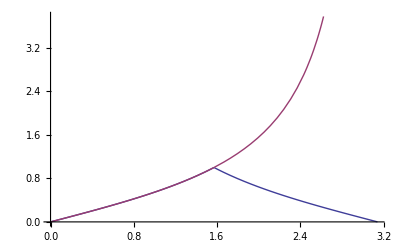

```mathematica
Plot[{(1-√(Cos[θ]^2))/Sin[θ],Tan[Abs[θ/2]]},{θ,0,Pi}]
```

```mathematica
Clear[k,B]
Phi[r_,θ_]:=B/2 r^k(1-√(Cos[θ]^2));
Simplify[Phi[r,θ]==Phi[2,Pi/2]]
```

B (2^k+r^k (-1+√(Cos[θ]^2)))==0

## magnitude of terms from EQ (32) - parabolic article

```mathematica
(*MF parameter - B*)MF=qe/me(xBB GG Mbh)/cc^4;(*RR parameter - k*)RR=qe^2/(me GG Mbh);
(* left side of 32 formula - forces:  *)
{(*first term*)MF,(*2nd term*)(RR)(MF),(*3rd term*)(RR)(MF)^2}
```

{0.00863869,1.64858×10^-21,1.42416×10^-23}

In SI units: 1 N = kg m s^2
In Base Units: 1 dyn= cm g s^-2
1 G= g^(1/2) cm^(-1/2) s^-1

```mathematica
me=9.109 10^-28 g;
GG=6.672×10^-8 cm^3 g^-1 s^-2;
cc=3 10^10 cm s^-1;
qe=4.803 10^-10 g^(1/2) cm^(3/2) s^-1;
Mbh=10 MS;
MS=1.989×10^33 g;



xBB=10 g^(1/2) cm^(-1/2) s^-1;{(*first term*)(GG Mbh qe xBB)/(cc^4 me),(*2nd term*)(qe^3 xBB)/(cc^4 me^2),(*3rd term*)(GG Mbh qe^4 xBB^2)/(cc^8 me^3)}
xBB=3 10^6 g^(1/2) cm^(-1/2) s^-1;{(*first term*)(GG Mbh qe xBB)/(cc^4 me),(*2nd term*)(qe^3 xBB)/(cc^4 me^2),(*3rd term*)(GG Mbh qe^4 xBB^2)/(cc^8 me^3)}
xBB=6 10^15 g^(1/2) cm^(-1/2) s^-1;{(*first term*)(GG Mbh qe xBB)/(cc^4 me),(*2nd term*)(qe^3 xBB)/(cc^4 me^2),(*3rd term*)(GG Mbh qe^4 xBB^2)/(cc^8 me^3)}
```

{8638.69,1.64858×10^-15,1.42416×10^-11}

{2.59161×10^9,4.94575×10^-10,1.28174}

{5.18321×10^18,0.989151,5.12698×10^18}

### forces in eq. (32)

```mathematica
xBB=10^8 g^(1/2) cm^(-1/2) s^-1;Mbh=10 MS;{(* RR II *)(qe^4 (xBB)^2)/(me^2 cc^4),(* Lorentz *)qe xBB,(* Gravity *) (me cc^4)/(GG Mbh),(* RR vs Lorentz *)(qe^3 (xBB))/(me^2 cc^4)}
```

{(7.91815×10^-10 cm g)/s^2,(0.04803 cm g)/s^2,(5.55987×10^-13 cm g)/s^2,1.64858×10^-8}

```mathematica
Mbh=10^9 MS;xBB=10^3 g^(1/2) cm^(-1/2) s^-1;{(* RR I *)(qe^3 xBB)/(me cc^2),(* RR II *)(qe^4 (xBB)^2)/(me^2 cc^4),(* Lorentz *)qe xBB,(* Gravity *) (me cc^4)/(GG Mbh),(* RR vs Lorentz *)(qe^3 (xBB))/(me^2 cc^4)}
```

{(1.35153×10^-19 cm^2 g)/s^2,(7.91815×10^-20 cm g)/s^2,(4.803×10^-7 cm g)/s^2,(5.55987×10^-21 cm g)/s^2,1.64858×10^-13}

```mathematica
xBB=10^16 g^(1/2) cm^(-1/2) s^-1;{(* RR I *)(qe^3 xBB)/(me cc^2),(* RR II *)(qe^4 (xBB)^2)/(me^2 cc^4),(* Lorentz *)qe xBB,(* Gravity *) (me cc^4)/(GG Mbh),(* RR vs Lorentz *)(qe^3 (xBB))/(me^2 cc^4)}
```

{(1.35153×10^-6 cm^2 g)/s^2,(7.91815×10^6 cm g)/s^2,(4.803×10^6 cm g)/s^2,(5.55987×10^-21 cm g)/s^2,1.64858}

### data for tab 3

```mathematica
Clear[ Mbh,xBB,cc,me,qe,GG];

me=9.109 10^-28 g;
GG=6.672×10^-8 cm^3 g^-1 s^-2;
cc=3 10^10 cm s^-1;
qe=4.803 10^-10 g^(1/2) cm^(3/2) s^-1;
Mbh=10 MS;
MS=1.989×10^33 g;

fceTAB3[xx_]:=(
xBB=10^xx g^(1/2) cm^(-1/2) s^-1;
(*Floor@Log[10,Abs[xx]]*)
{xx,{(*first term*)Round[RealExponent[(GG Mbh qe xBB)/(cc^4 me)]],
(*2nd term*)Round[RealExponent[(qe^3 xBB)/(cc^4 me^2)]],
(*3rd term*)Round[RealExponent[(GG Mbh qe^4 xBB^2)/(cc^8 me^3)]]},
{(GG Mbh qe xBB)/(cc^4 me),(qe^3 xBB)/(cc^4 me^2),(GG Mbh qe^4 xBB^2)/(cc^8 me^3)}
}

);
fceTAB3[15.8]
fceTAB3[12]
fceTAB3[8]
fceTAB3[6.4]
fceTAB3[4]
fceTAB3[0]
fceTAB3[-2.9]
fceTAB3[-5]
```

{15.8,{19,0,19},{5.45064×10^18,1.04019,5.66969×10^18}}

{12,{15,-4,11},{8.63869×10^14,0.000164858,1.42416×10^11}}

{8,{11,-8,3},{8.63869×10^10,1.64858×10^-8,1424.16}}

{6.4,{9,-9,0},{2.16994×10^9,4.14106×10^-10,0.898585}}

{4,{7,-12,-5},{8.63869×10^6,1.64858×10^-12,0.0000142416}}

{0,{3,-16,-13},{863.869,1.64858×10^-16,1.42416×10^-13}}

{-2.9,{0,-19,-19},{1.08755,2.07545×10^-19,2.25714×10^-19}}

{-5,{-2,-21,-23},{0.00863869,1.64858×10^-21,1.42416×10^-23}}

Effective potential

## FIG. 1.

```mathematica
Phi[r_,θ_]:=BB r^kuk(1-√(Cos[θ]^2));qAt[r_,θ_]:=0; qAϕ[r_,θ_]:=Phi[r,θ];
Br=Simplify[D[Phi[r,θ],θ]/(r^2 Sin[θ])];Bθ=Simplify[-D[Phi[r,θ],r]/(r Sin[θ])];
field=Simplify[TransformedField["Spherical"-> "Cartesian",{Br,Bθ,0},{r,θ,ϕ}->{x,y,z}]/.y->0];
fieldXZ={field[[1]],field[[3]]};{fieldXZ1,fieldXZ2}={fieldXZ,fieldXZ};

Clear[kuk,BB]
Simplify[fieldXZ1[[1]]^2+fieldXZ2[[1]]^2,x>0&&z>0]

BB=1;kuk=3/4;

pic=Show[
ContourPlot[ Abs[Phi[√(x^2+z^2),ArcTan[x/z]]],{x,-15.5,15.5},{z,-15.5,15.5},ContourShading->None,Contours->10,WorkingPrecision->77,ContourStyle->{Black}],
ContourPlot[ Abs[Phi[√(x^2+z^2),ArcTan[x/z]]]==Phi[RH,Pi/2],{x,-15.5,15.5},{z,-15.5,15.5},ContourStyle->{{Black,Dashed,Thick}}],
StreamPlot[If[z>0,fieldXZ1,fieldXZ2],{x,-21,21},{z,-21,21},StreamPoints->Coarse,StreamStyle->Pink,StreamScale->0.15],
AspectRatio->1,Axes->True,RotateLabel->False,BaseStyle->{15,Background->White},FrameLabel->{x,z},ImageSize->400,RotateLabel->False,
Prolog->{Gray,EdgeForm[{JoinForm["Round"],Gray,Thickness[0.05]}], Polygon[{{-20,-1},{-6,-0.1},{-6,0.1},{-20,1}}], Polygon[{{20,-1},{6,-0.1},{6,0.1},{20,1}}]},
Epilog->{Text["corona",{12,7}],Text["jet\n funnel",{3,10}],Rotate[Text["accretion disk",{11.3,-2.5}],-0.07],Gray,Rotate[Text["magnetic field lines",{-3,9}],-1.3],White,Disk[{0,0},2],Black,Circle[{0,0},2],Text["BH",{0.1,-0.1}]}
]
```

((4 x^2+3 z (z-√(x^2+z^2)))^2)/(8 x^2 (x^2+z^2)^(9/4))

```mathematica
(*Export["fig1.png",pic];*)
Export["fig1.pdf",pic];
```

```mathematica
Clear[kuk,BB]
Simplify[fieldXZ1[[1]]^2+fieldXZ2[[1]]^2,x>0&&z>0]
```

(B^2 (x^2+z^2)^(-3+k) (x^2+k z (z-√(x^2+z^2)))^2)/(2 x^2)

## FIG. 2. - effective potential - B>0 and B<0 - MK

```mathematica
BB=-0.1;LL=3.7;kuk=3/4;Energie=0.9701;eRange={0.964,1.004};x0=15;
sol=FindMinimum[Veff[√(x^2+z^2),ArcTan[x/z],LL],{x,6},{z,0.1}];EE0=sol[[1]];{x0,z0}={x,z}/.sol[[2]]
picA=Plot3D[Veff[√(x^2+z^2),ArcTan[x/z],LL],{x,0,21},{z,-11.5,11.5},PlotPoints->40,PlotRange->eRange,ImageSize->450,BaseStyle->15,AxesEdge->{{0,0},{1,-1},{0,0}},Ticks->{Automatic,Automatic,Automatic},Boxed->True,AxesLabel->{"x","z",ce},MeshStyle->{Black,Thick,Dashed},MeshShading->GrayLevel/@Range[0.6,1,0.2],Mesh->{{{Energie}}},MeshFunctions->{#3&},Lighting->"Neutral",Epilog->{Text[Style["ℬ < 0",20],Scaled[{0.5,0.9}]]}];
picB1=Plot[{Veff[x,Pi/2,LL],Energie},{x,0,21},PlotRange->eRange,PlotStyle->{{Black,Thick},{Black,Dashed}},AspectRatio->1,Frame->True,ImageSize->225,BaseStyle->15,FrameLabel->{"x",ce},RotateLabel->False,Epilog->{Text["z = 0",Scaled[{0.5,0.8}]]}];
picB2=Plot[{Veff[√(x0^2+z^2),ArcTan[x0/z],LL],Energie},{z,-11.5,11.5},PlotRange->eRange,PlotStyle->{{Black,Thick},{Black,Dashed}},AspectRatio->1,Frame->True,ImageSize->225,BaseStyle->{15,Background->White},FrameLabel->{"z",ce},RotateLabel->False,Epilog->{Text[Row[{"x = ",Round[x0,0.1]}],Scaled[{0.5,0.8}]]}];
pic=Grid[{{picA,SpanFromLeft},{SpanFromAbove,SpanFromBoth},{picB1,picB2}},Spacings->{1,1}]
```

```mathematica
Export["fig2a.png",pic];
```

```mathematica
B=0.1;BB=B;LL=4.18;kuk=3/4;Energie=0.955;eRange={0.947,1.004};
sol=FindMinimum[Veff[√(x^2+z^2),ArcTan[x/z],LL],{x,6},{z,0.1}];EE0=sol[[1]];{x0,z0}={x,z}/.sol[[2]]
picA=Plot3D[Veff[√(x^2+z^2),ArcTan[x/z],LL],{x,0,21},{z,-11.5,11.5},PlotPoints->40,PlotRange->eRange,ImageSize->450,BaseStyle->15,AxesEdge->{{0,0},{1,-1},{0,0}},Epilog->{Text[Style["ℬ > 0",20],Scaled[{0.5,0.9}]]},Ticks->{Automatic,Automatic,Automatic},Boxed->True,AxesLabel->{"x","z",ce},MeshStyle->{Black,Thick,Dashed},MeshShading->GrayLevel/@Range[0.6,1,0.2],Mesh->{{{Energie}}},MeshFunctions->{#3&},Lighting->"Neutral"];
picB1=Plot[{Veff[x,Pi/2,LL],Energie},{x,0,21},PlotRange->eRange,PlotStyle->{{Black,Thick},{Black,Dashed}},AspectRatio->1,Frame->True,ImageSize->225,BaseStyle->15,FrameLabel->{"x",ce},RotateLabel->False,Epilog->{Text["z = 0",Scaled[{0.5,0.8}]]}];
picB2=Plot[{Veff[√(x0^2+z^2),ArcTan[x0/z],LL],Energie},{z,-11.5,11.5},PlotRange->eRange,PlotStyle->{{Black,Thick},{Black,Dashed}},AspectRatio->1,Frame->True,ImageSize->225,BaseStyle->{15,Background->White},FrameLabel->{"z",ce},RotateLabel->False,Epilog->{Text[Row[{"x = ",Round[x0,0.1]}],Scaled[{0.5,0.8}]]}];
pic=Grid[{{picA,SpanFromLeft},{SpanFromAbove,SpanFromBoth},{picB1,picB2}},Spacings->{1,1}]
```

```mathematica
Export["fig2b.png",pic];
```

## FIG. 3. - ISCO off eq. plane !!! B < 0 !!! MS

```mathematica
Clear[kuk,fceMINoff];

xoffLL[r_,BB_,k_]:=(BB (6+k (-2+r)-2 r) r^k-√(-4 (3-r) r^2+BB^2 (6+k (-2+r)-2 r)^2 r^(2 k)))/(2 (3-r));fISCO[r_,B_,k_]:=(B (6+k (-2+r)-2 r) r^k-√(4 (-3+r) r^2+B^2 (6+k (-2+r)-2 r)^2 r^(2 k))+(3-r) (B k (6+k (-2+r)-2 r) r^(-1+k)+B (-2+k) r^k-(8 (-3+r) r+4 r^2+2 B^2 (-2+k) (6+k (-2+r)-2 r) r^(2 k)+2 B^2 k (6+k (-2+r)-2 r)^2 r^(-1+2 k))/(2 √(4 (-3+r) r^2+B^2 (6+k (-2+r)-2 r)^2 r^(2 k)))));
xθmin[r_,BB_,LL_,k_]:=ArcCos[(BB r^k)/(-LL+BB r^k)];
θmin[r_,BB_,k_]:=ArcCos[(BB r^k)/(-xoffLL[r,BB,k]+BB r^k)];


fceMINoffz[kuk_,BBlist_]:=(
RH=2;
fceEX[r_,θ_,B_,k_]:=r^2+2 B^2 (-2+r) r^(2 k) (-1+(-1+k) Cos[θ]) Sec[θ]^2 Sin[θ/2]^2+B^2 r^(2 k) Tan[θ]^2;
ISCOdata=Table[
{R0=r/.NSolve[fISCO[r,BB,kuk]==0,r][[1]],θmin[R0,BB,kuk]}
,{BB,-0.49,-0.01,0.01}];

(*ISCOdata=Prepend[ISCOdata,{6,0.0069171}];
ISCOdata=Append[ISCOdata,{6,Pi/2}];*)
ISCOdata=Append[ISCOdata,{6,Pi/2}];

text={};ii=0;

Show[
BB=-0.05;ii++;RT=20;θT=θ/.FindRoot[fceEX[RT,θ,BB,kuk]==0,{θ,If[ii<2,1.5,1]}];
AppendTo[text,Text[BB,Reverse[FromPolarCoordinates[{RT,θT}],1]]];
ContourPlot[fceEX[√(x^2+z^2),ArcCos[z/√(x^2+z^2)],BB,kuk]==0,{x,6.5,31},{z,0,31},ContourStyle->{Black}],
BB=-0.2;ii++;RT=22;θT=θ/.FindRoot[fceEX[RT,θ,BB,kuk]==0,{θ,If[ii<2,1.5,1]}];
AppendTo[text,Text[BB,Reverse[FromPolarCoordinates[{RT,θT}],1]]];
ContourPlot[fceEX[√(x^2+z^2),ArcCos[z/√(x^2+z^2)],BB,kuk]==0,{x,8,31},{z,0,31},ContourStyle->{Black}],
BB=-0.4;ii++;RT=22;θT=θ/.FindRoot[fceEX[RT,θ,BB,kuk]==0,{θ,If[ii<2,1.5,1]}];
AppendTo[text,Text[BB,Reverse[FromPolarCoordinates[{RT,θT}],1]]];
ContourPlot[fceEX[√(x^2+z^2),ArcCos[z/√(x^2+z^2)],BB,kuk]==0,{x,12,31},{z,0,31},ContourStyle->{Black}],
ListPlot[Reverse[FromPolarCoordinates[ISCOdata],2],Joined->True,PlotStyle->{{Black,Dotted}}],
ContourPlot[ {(x^2+z^2)^(kuk/2)(1-√(z^2/(x^2+z^2)))==RH^kuk},{x,0,31},{z,0,31},ContourStyle->{{Dashed,Black},Red}],
FrameLabel->{"x","z"},ImageSize->300,BaseStyle->{15,Background->White},RotateLabel->False,Frame->True,AspectRatio->1,PlotRange->{{0,25.1},{0,25.1}},Epilog->{text,Text[Row[{"w"," = ",kuk}],Scaled[{0.5,0.9}]],LightGray,Disk[{0,0},2]}
]
);
fceMINoff[kuk_,BBlist_,POINT_]:=(
RH=2;
fceEX[r_,θ_,B_,k_]:=r^2+2 B^2 (-2+r) r^(2 k) (-1+(-1+k) Cos[θ]) Sec[θ]^2 Sin[θ/2]^2+B^2 r^(2 k) Tan[θ]^2;
ISCOdata=Table[
{R0=r/.NSolve[fISCO[r,BB,kuk]==0,r][[1]],θmin[R0,BB,kuk]}
,{BB,-10,-0.1,0.1}];

ISCOdata=Prepend[ISCOdata,POINT];
ISCOdata=Append[ISCOdata,{6,Pi/2}];

text={};ii=0;

Show[
Table[
ii++;RT=20;θT=θ/.FindRoot[fceEX[RT,θ,BB,kuk]==0,{θ,If[ii<2,1.5,1]}];
AppendTo[text,Text[BB,Reverse[FromPolarCoordinates[{RT,θT}],1]]];
ContourPlot[fceEX[√(x^2+z^2),ArcCos[z/√(x^2+z^2)],BB,kuk]==0,{x,0,31},{z,0,31},ContourStyle->{Black}],
{BB,BBlist}],
ListPlot[Reverse[FromPolarCoordinates[ISCOdata],2],Joined->True,PlotStyle->{{Black,Dotted}},Filling->Axis,FillingStyle->White],
ContourPlot[ (x^2+z^2)^(kuk/2)(1-√(z^2/(x^2+z^2)))==RH^kuk,{x,0,31},{z,0,31},ContourStyle->{{Dashed,Black}}],
FrameLabel->{"x","z"},ImageSize->300,BaseStyle->{15,Background->White},RotateLabel->False,Frame->True,AspectRatio->1,PlotRange->{{0,25.1},{0,25.1}},Epilog->{text,Text[Row[{"w"," = ",kuk}],Scaled[{0.5,0.9}]],LightGray,Disk[{0,0},2]}
]
);
point1={6,0.0069171};point2={18,0.0013731};
pic=GraphicsRow[{fceMINoff[0.,{-0.5,-2,-5,-10,-50},point1],fceMINoff[0.75,{-0.1,-0.5,-1,-2,-5},point2],fceMINoffz[1,{-0.05,-0.2,-0.4}]},Spacings->0,ImageSize->900]
```

```mathematica
Export["fig3.pdf",pic];
```

### extra - we can plot PS sections out of eq.plane

```mathematica
θ0=1.29;
Show[pic,Plot[{-2+Cos[θ0]x,Cos[1.4]x},{x,0,31}]]
```

```mathematica
(* Poincare sections throught special line *)
```

```mathematica
Simplify[fceEX[r,θ,-0.1,3/4]==0]
```

r^(3/2) (√r-0.005 (-2.+r) (4.+Cos[θ]) Sec[θ]^2 Sin[θ/2]^2+0.01 Tan[θ]^2)==0

```mathematica
Simplify[fceEX[r,θ,B,kuk]==0]
```

r^2+0.02 (-2+r) r^(2 kuk) (-1+(-1+kuk) Cos[θ]) Sec[θ]^2 Sin[θ/2]^2+0.01 r^(2 kuk) Tan[θ]^2==0

## FIG. 4. - ISCO in eq. plane !!! B > 0 !!!

```mathematica
Clear[r,B,k];FullSimplify[D[fLL[r,B,k],r]]
```

(B (6+k (-2+r)-2 r) r^k-√(4 (-3+r) r^2+B^2 k^2 (-2+r)^2 r^(2 k))+(-3+r) (-B k (6+k (-2+r)-2 r) r^(-1+k)-B (-2+k) r^k+((-2+r) (6 r^2+B^2 k^2 r^(2 k) (k (-2+r)+r)))/(r √(4 (-3+r) r^2+B^2 k^2 (-2+r)^2 r^(2 k)))))/(2 (-3+r)^2)

```mathematica
nullPARA[r_,B_,k_]:=(B (6+k (-2+r)-2 r) r^k √(4 (-3+r) r^2+B^2 k^2 (-2+r)^2 r^(2 k))-(4 (-3+r) r^2+B^2 k^2 (-2+r)^2 r^(2 k))+(-3+r) (√(4 (-3+r) r^2+B^2 k^2 (-2+r)^2 r^(2 k))(-B k (6+k (-2+r)-2 r) r^(-1+k)-B (-2+k) r^k)+((-2+r) (6 r^2+B^2 k^2 r^(2 k) (k (-2+r)+r)))/r));

pic=ContourPlot[{nullPARA[r,10^b,0]==0,nullPARA[r,10^b,0.75]==0,nullPARA[r,10^b,1]==0,nullPARA[r,10^b,0.1]==0},{r,2,7},{b,Log[10,0.005],Log[10,250]},PlotPoints->50,BaseStyle->{15,Background->White},ImageSize->350,PlotRange->{{1.6,7.3},{Log[10,0.005],Log[10,200]}},FrameLabel->{"r",cb},RotateLabel->False,ContourStyle->{{Black,DotDashed},{Black},{Black,Dashed},Dotted},Exclusions->{{r==3}},Epilog->{Text[Row[{"w"," = 0"}],Scaled[{0.78,0.9}]],Text[Row[{"w"," = 0.1"}],Scaled[{0.5,0.8}]],Text[Row[{"w"," = 3/4"}],Scaled[{0.35,0.63}]],Text[Row[{"w"," = 1"}],Scaled[{0.2,0.45}]],Dotted,Line[{{2,Log[10,0.001]},{2,Log[10,300]}}]},FrameTicks->{{Table[{y,ToString[Round[10^y,0.001]]},{y,Log[10,0.001],Log[10,100]}],Automatic},{Automatic,Automatic}}]
```

```mathematica
Export["fig4.pdf",pic];
```

## FIG. 5. - Energy in effective potential minima

```mathematica
Clear[r,θ,B,L,kuk,dataISCO];
fceEX[r_,θ_,B_,k_]:=r^2+2 B^2 (-2+r) r^(2 k) (-1+(-1+k) Cos[θ]) Sec[θ]^2 Sin[θ/2]^2+B^2 r^(2 k) Tan[θ]^2;

F[r_,B_,k_]:=B r^k(6-2k +k r-2 r);
offLL[r_,B_,k_]:=(F[r,B,k]-√(4 (r-3) r^2+F[r,B,k]^2))/(2 (3-r));
inLL[r_,B_,k_]:=(F[r,B,k]-√(4 (r-3) r^2+B^2 k^2 (r-2)^2 r^(2 k)))/(2 (3-r));
nullPARA[r_,B_,k_]:=B (6+k (-2+r)-2 r) r^k-√(4 (-3+r) r^2+B^2 k^2 (-2+r)^2 r^(2 k))+(3-r) (B k (6+k (-2+r)-2 r) r^(-1+k)+B (-2+k) r^k+((-2+r) (-6 r^2-B^2 k^2 r^(2 k) (k (-2+r)+r)))/(r √(4 (-3+r) r^2+B^2 k^2 (-2+r)^2 r^(2 k))));
nVeff[r_,θ_,B_,L_,kuk_]:=√(-gtt[r,θ](1+gUϕϕ[r,θ] (L-B r^kuk(1-√(Cos[θ]^2)))^2));

kuk=3/4;θ0=Pi/2;tabB={B0,B1,B2,B3,B4}={0,0.1,0.5,1,100};
fE[r_,B_]:=nVeff[r,θ0,B,inLL[r,B,kuk],kuk];

dataISCO=Table[rISCO=r/.FindRoot[nullPARA[r,tabB[[i]],kuk],{r,5}];{rISCO,fE[rISCO,tabB[[i]]]},{i,1,Length[tabB]}];
figOffData={};

Table[
data=Table[θT=θ/.FindRoot[fceEX[r,θ,BB,kuk]==0,{θ,1}];{r,nVeff[r,θT,BB,offLL[r,BB,kuk],kuk]},{r,Table[N[10^m],{m,0.6,1.8,0.02}]}];
sorted=Sort[data,#1[[2]]<#2[[2]]&]; 
dataISCO=Prepend[dataISCO,sorted[[1]]];
figOffData=Append[figOffData,data];,
{BB,{-0.1,-0.2,-0.3,-0.5,-0.7,-1,-100}}
];

fitISCO[r_]=Fit[dataISCO,{1,r,r^2,1/r,1/r^2},r];

pic=Show[
LogLinearPlot[{1,If[r<18.5,fitISCO[r]],fE[r,B0],fE[r,B1],fE[r,B2],fE[r,B3],fE[r,B4]},{r,1.5,55},PlotRange->{{1.9,50},{0.79,1.01}},PlotStyle->{{Black,Dotted},{Black,Dashed},{Black,Thick},Black,Black,Black,Black,Black},AspectRatio->1,Frame->True,ImageSize->350,BaseStyle->{15,Background->White},FrameLabel->{"r",ce},RotateLabel->False,
Epilog->{PointSize->0.01,Point[dataISCO],Text["ISCO",Scaled[{0.21,0.07}]],Text["-100",Scaled[{0.5,0.97}]],Text["-1",Scaled[{0.41,0.93}]],Text["-0.5",Scaled[{0.35,0.87}]],Text["-0.1",Scaled[{0.32,0.8}]],Text["0",Scaled[{0.3,0.71}]],Text["0.1",Scaled[{0.25,0.65}]],Text["0.5",Scaled[{0.22,0.5}]],Text["1",Scaled[{0.17,0.3}]],Text["10",Scaled[{0.4,0.2}]]}],
ListLogLinearPlot[{figOffData[[1]],figOffData[[4]],figOffData[[6]],figOffData[[7]]},Joined->True,PlotRange->{{1.9,55},{0.79,1.01}},PlotStyle->{Black}]
]
```

```mathematica
Export["fig5.pdf",pic];
```

Charged Particle Trajectories

## def > GiveMeTrajectory[k_,BB_,LL_,R0_,θ0_,xEND_]

```mathematica
Clear[BB,k,kuk,RH,B,Rend,R0,θ0,LL,EE,metoda,stepsize,colour,Aϕ,oblast1D,oblast2D,oblast3D,GiveMeTrajectory,TatraTra,errLimt,konec]

qAt[r_,θ_]:=0; qAϕ[r_,θ_]:=BB r^kuk(1-Cos[θ]);
Veff[r_,θ_,L_]:=qAt[r,θ]+√(-gtt[r,θ](1+gUϕϕ[r,θ] (L-qAϕ[r,θ])^2));
GiveMeTrajectory[k_,BB_,LL_,R0_,θ0_,xEND_]:=( (*  odpovida rovnicim  Du^α/dτ -Subscript[f, L]^α -Subscript[f, rad]^α = 0  *)
Clear[r,θ,ϕ,t,ur,uth,uph,ut,EE,rovniceUP,draha];
M=1;

rovniceUP={-BB kuk (-1+√(Cos[θ[τ]]^2)) (2 M-r[τ]) r[τ]^(-2+kuk) Uph[τ]+(2 M-r[τ]) Sin[θ[τ]]^2 Uph[τ]^2+(M Ur[τ]^2)/(2 M r[τ]-r[τ]^2)+(M (-2 M+r[τ]) Ut[τ]^2)/r[τ]^3+(2 M-r[τ]) Uth[τ]^2-1/2 BB k r[τ]^(-5+kuk) (2 BB kuk^2 (-1+√(Cos[θ[τ]]^2))^2 Csc[θ[τ]]^2 (2 M-r[τ]) r[τ]^kuk Ur[τ]-2 kuk (-1+√(Cos[θ[τ]]^2)) r[τ]^2 ((5-2 kuk) M+(-2+kuk) r[τ]) Uph[τ] Ur[τ]+2 BB kuk^2 (-1+√(Cos[θ[τ]]^2))^2 (2 M-r[τ]) r[τ]^(2+kuk) Uph[τ]^2 Ur[τ]-2 BB r[τ]^(3+kuk) Sin[θ[τ]]^2 Uph[τ]^2 Ur[τ]-2 BB kuk^2 (-1+√(Cos[θ[τ]]^2))^2 Csc[θ[τ]]^2 r[τ]^(1+kuk) Ur[τ]^3-(2 BB kuk (-1+√(Cos[θ[τ]]^2)) Cot[θ[τ]] (2 M-r[τ]) r[τ]^(1+kuk) Uth[τ])/(√(Cos[θ[τ]]^2))+((1+2 kuk (-1+√(Cos[θ[τ]]^2))-Cos[2 θ[τ]]) Cot[θ[τ]] (2 M-r[τ]) r[τ]^3 Uph[τ] Uth[τ])/(√(Cos[θ[τ]]^2))-2 (√(Cos[θ[τ]]^2)+kuk (-1+√(Cos[θ[τ]]^2)) Cot[θ[τ]]^2) (2 M-r[τ]) r[τ]^3 Tan[θ[τ]] Uph[τ] Uth[τ]+(4 BB kuk (-1+√(Cos[θ[τ]]^2)) Cot[θ[τ]] r[τ]^(2+kuk) Ur[τ]^2 Uth[τ])/(√(Cos[θ[τ]]^2))-2 BB r[τ]^(3+kuk) Ur[τ] Uth[τ]^2)+Ur'[τ],-BB √(Cos[θ[τ]]^2) r[τ]^(-2+kuk) Tan[θ[τ]] Uph[τ]-Cos[θ[τ]] Sin[θ[τ]] Uph[τ]^2+(2 Ur[τ] Uth[τ])/r[τ]-1/(2 √(Cos[θ[τ]]^2))BB k r[τ]^(-5+kuk) (2 BB kuk^2 (2 Cot[θ[τ]]^2-√(Cos[θ[τ]]^2) (1+Cos[θ[τ]]^2) Csc[θ[τ]]^2) r[τ]^(1+kuk) Ur[τ]^2 Uth[τ]-r[τ] Uth[τ] (kuk (-1+2 √(Cos[θ[τ]]^2)-Cos[2 θ[τ]]) (2 M-r[τ]) r[τ] Uph[τ]+2 BB r[τ]^(1+kuk) (2 kuk^2 Cos[θ[τ]]^2 (2 M-r[τ])+√(Cos[θ[τ]]^2) (-kuk^2 Cos[θ[τ]]^2 (2 M-r[τ])+kuk^2 (-2 M+r[τ])+r[τ] Sin[θ[τ]]^2)) Uph[τ]^2+2 BB √(Cos[θ[τ]]^2) r[τ]^kuk (1+r[τ]^2 Uth[τ]^2))+Cot[θ[τ]] Ur[τ] ((-3+2 kuk √(Cos[θ[τ]]^2)+(3-2 kuk) Cos[2 θ[τ]]) r[τ]^2 Uph[τ]+2 BB kuk (-1+√(Cos[θ[τ]]^2)) r[τ]^kuk (1+2 r[τ]^2 Uth[τ]^2)))+Uth'[τ],BB Csc[θ[τ]] r[τ]^(-3+kuk) Sec[θ[τ]] (-kuk (-1+√(Cos[θ[τ]]^2)) Cot[θ[τ]] Ur[τ]+√(Cos[θ[τ]]^2) r[τ] Uth[τ])+(2 Uph[τ] (Ur[τ]+Cot[θ[τ]] r[τ] Uth[τ]))/r[τ]-BB k r[τ]^(-6+kuk) (BB kuk^2 (-1+√(Cos[θ[τ]]^2))^2 Csc[θ[τ]]^2 (2 M-r[τ]) r[τ]^(1+kuk) Uph[τ]-BB r[τ]^(2+kuk) Uph[τ]+BB kuk^2 (-1+√(Cos[θ[τ]]^2))^2 (2 M-r[τ]) r[τ]^(3+kuk) Uph[τ]^3-BB r[τ]^(4+kuk) Sin[θ[τ]]^2 Uph[τ]^3+(kuk (-1+√(Cos[θ[τ]]^2)) Csc[θ[τ]]^2 r[τ]^2 ((5-2 kuk) M+(-2+kuk) r[τ]) Ur[τ]^2)/(-2 M+r[τ])-BB kuk^2 (-1+√(Cos[θ[τ]]^2))^2 Csc[θ[τ]]^2 r[τ]^(2+kuk) Uph[τ] Ur[τ]^2+kuk M (-1+√(Cos[θ[τ]]^2)) Csc[θ[τ]]^2 (2 M-r[τ]) Ut[τ]^2+(Cot[θ[τ]] (1-kuk-kuk Cot[θ[τ]]^2+kuk √(Cos[θ[τ]]^2) Csc[θ[τ]]^2) r[τ]^3 Ur[τ] Uth[τ])/(√(Cos[θ[τ]]^2))-(-2+kuk) √(Cos[θ[τ]]^2) Csc[θ[τ]] r[τ]^3 Sec[θ[τ]] Ur[τ] Uth[τ]+2 BB kuk √(Cos[θ[τ]]^2) (-1+√(Cos[θ[τ]]^2)) Csc[θ[τ]] r[τ]^(3+kuk) Sec[θ[τ]] Uph[τ] Ur[τ] Uth[τ]-kuk (-1+√(Cos[θ[τ]]^2)) Csc[θ[τ]]^2 (2 M-r[τ]) r[τ]^3 Uth[τ]^2-BB r[τ]^(4+kuk) Uph[τ] Uth[τ]^2)+Uph'[τ],-(2 M Ur[τ] Ut[τ])/(2 M r[τ]-r[τ]^2)-BB k r[τ]^(-4+kuk) Ut[τ] (-kuk M (-1+√(Cos[θ[τ]]^2)) r[τ] Uph[τ]-BB r[τ]^(1+kuk) (-kuk^2 Cos[θ[τ]]^2 (2 M-r[τ])+kuk^2 (-1+2 √(Cos[θ[τ]]^2)) (2 M-r[τ])+r[τ] Sin[θ[τ]]^2) Uph[τ]^2-BB r[τ]^kuk (1/2 kuk^2 (3-4 √(Cos[θ[τ]]^2)+Cos[2 θ[τ]]) Csc[θ[τ]]^2 Ur[τ]^2+2 kuk r[τ] (-Cot[θ[τ]]+√(Cos[θ[τ]]^2) Csc[θ[τ]] Sec[θ[τ]]) Ur[τ] Uth[τ]+r[τ]^2 Uth[τ]^2))+Ut'[τ]};


EE=Veff[R0,θ0,LL];

(* automaticky
rovnice=((eqmoLo)
/.Ur[τ]->gup[[1,1]]ur[τ]/.Uth[τ]->gup[[2,2]]uth[τ]/.Uph[τ]->gup[[3,3]]uph[τ] /.Ut[τ]->gup[[4,4]]ut[τ]
/.r->r[τ]/.θ->θ[τ]/.ph->ϕ[τ]);
*)
(*---- rovnice pohybu vcetne radice ----*)


(*---- Equations of motion + initial conditions ----*)
Equations ={(* ur[τ] = Subscript[u, r](τ).... *)
r'[τ]==Ur[τ],rovniceUP[[1]]==0 ,
θ'[τ]==Uth[τ],rovniceUP[[2]]==0,
ϕ'[τ]==Uph[τ],rovniceUP[[3]]==0,
t'[τ]==Ut[τ],rovniceUP[[4]]==0
};

IntCond ={r[0]    == R0, Ur[0]   ==  0,θ[0]   == θ0, Uth[0]  == 0,ϕ[0]   == 0,
Uph[0]  ==gUϕϕ[R0,θ0] (LL-qAϕ[R0,θ0])(*uph[0]  == LL-qAϕQ[r0,θ0,aa,xBB,QQ]*),t[0]==0,Ut[0]== gUtt[R0,θ0](-EE)};
(*---- Equations of motion + initial conditions ----*)

(*---- trajectory calculation ----*)
time1=SessionTime[];
data=Reap[NDSolve[{Equations,IntCond},{r,Ur,θ,Uth,ϕ,Uph,t,Ut},{τ,0,xEND},{Method->{"EventLocator","Event"->{θ[τ]-Pi/2,r[τ]-Rend,r[τ]-xInfinity},"EventAction":>{Sow[{r[τ],grr[r[τ],θ[τ]]Ur[τ],τ}],Throw[ Null,"StopIntegration"],Throw[Null, "StopIntegration"]},"Method"->metoda},{StartingStepSize->stepsize,MaxSteps->∞}}]];
time2=SessionTime[];

draha=data[[1]];(* here trajectory will be located *)
ipub=r/.draha[[1,1]];domain=ipub["Domain"];{begin,end} = domain[[1]];
(*---- trajectory calculation ----*)


(*---- Poincare surface of section + Winding number ----*)
If[data[[-1]]!={},
psdataT=Take[data[[-1,1]],{1,-1,2}];(* Poincare surface of section with time stamp*)
psdata=psdataT[[All,1;;2]];
,psdata={}]; (* Poincare surface of section *)

If[psdata!={},
centralPoint=Mean[psdata];centralPoint={centralPoint[[1]],0};len=Length[psdata];
seqOfAng=Table[PlanarAngle[{psdata[[i+1]],centralPoint,psdata[[i]]}],{i,1,len-1,1}];
rwn=N[Mean[seqOfAng]/(2 Pi)];(* winding number*)
seqOfAngT=Transpose[{Take[psdataT[[All,3]],{1,len-1}],seqOfAng/2Pi}];(* angles wit timestamp *),
seqOfAngT={};
];
(*---- Poincare surface of section + Winding number ----*)

(*--------------- Frequencies -----------------------*)
Clear[dataR,dataT,dataK,fminK,fminR,fminT,uUt2];
{fminK,fminR,fminT}={0,0,0};(* fail safe condition - give there some initial values *)
uUt2=(-1/gtt[R0, θ0]EE)^2;
dataR=Table[Evaluate[r[i]/.draha][[1]],{i,1, end}];(* create the series of numbere from radial coordinate - "dataR" *)
XdataR=2Abs[Fourier[dataR,FourierParameters->{-1,1}]];(* Fourier transform will be applied to this number series "dataR" - Fourier spectra "XdataR" will be genearted *)
FdataR=Table[{(i-1)/( end),XdataR[[i]]},{i,1,Round[Length[dataR]/2]}];(* resacling the spectra "XdataR" *)
FdataR=Delete[FdataR,1];(* delete first term from the Fourier spectra *)
fminR=2Pi Cases[FdataR,{_,Max@FdataR[[All,2]]}][[1,1]];(* finding the maximal value in Fourier spectra - finding where the peak is located *)

dataT=Table[Evaluate[θ[i]/.draha][[1]],{i,1, end}];XdataT=2Abs[Fourier[dataT,FourierParameters->{-1,1}]];
FdataT=Table[{(i-1)/( end),XdataT[[i]]},{i,1,Round[Length[dataT]/2]}];
FdataT=Delete[FdataT,1];
fminT=2Pi Cases[FdataT,{_,Max@FdataT[[All,2]]}][[1,1]];

dataK=Table[Evaluate[Cos[ϕ[i]]/.draha][[1]],{i,1, end}];XdataK=2Abs[Fourier[dataK,FourierParameters->{-1,1}]];
FdataK=Table[{(i-1)/( end), XdataK[[i]]},{i,1,Round[Length[dataK]/2]}];
FdataK=Delete[FdataK,1];
fminK=2Pi Cases[FdataK,{_,Max@FdataK[[All,2]]}][[1,1]];
(*--------------- Frequencies -----------------------*)


{draha,end,psdata}

);

ShowTrajectory[colour_]:=(
(* this function will show particle trajectory
colour = particle trajectory colour; 
black dashed = boundary for the particle motion, AKA energy boundary fuction AKA curve of zero velocity;
gray curves = magnetic field lines *)
ImPd={{45,1},{45,1}};

pic1=ParametricPlot[ {XXX[r[τ],θ[τ],ϕ[τ]], YYY[r[τ],θ[τ],ϕ[τ]] }/.draha,{τ,begin,fix end},PlotStyle->{colour},Frame->True,BaseStyle->fontyW,PlotRange->oblast2D,Epilog->{PointSize[0.02],Point[{XXX[R0,θ0,0],YYY[R0,θ0,0]}],LightGray,Disk[{0,0},RH]},FrameLabel->{"x","y"},RotateLabel->False,Axes->False,ImageSize->ImSz,ImagePadding->ImPd,PerformanceGoal->"Speed",MaxRecursion->10];

pic2=ParametricPlot[ {XXX[r[τ],θ[τ],ϕ[τ]],ZZZ[r[τ],θ[τ],ϕ[τ]] }/.draha,{τ,begin,fix end},PlotStyle->{colour},Frame->True,BaseStyle->fontyW,PlotRange->oblast2D,Prolog->{LightGray,Disk[{0,0},RH]},FrameLabel->{"x","z"},RotateLabel->False,Axes->False,ImageSize->ImSz,ImagePadding->ImPd,
Epilog->{PointSize[0.02],Point[{XXX[R0,θ0,0],ZZZ[R0,θ0,0]}],
Text[Row[{ce,"≐",Round[EE,0.001],", ",cl,"≐",Round[LL,0.001]}],Scaled[{0.5,0.9}]],
Text[Row[{"r_0≐",Round[R0,0.01],", θ_0≐",Round[θ0,0.01],", (ϕ̇)_0≐",Round[ϕ'[0]/.draha[[1]],0.01]}],Scaled[{0.5,0.1}]]
}];

pic3=Show[
ParametricPlot[ {XXX[r[τ],θ[τ],0],ZZZ[r[τ],θ[τ],0] }/.draha,{τ,begin, fix end},PlotStyle->{colour},Frame->True,BaseStyle->fontyW,PerformanceGoal->"Speed",MaxRecursion->10,PlotRange->{{0,oblast1D[[2]]},{oblast1D[[1]]/2,oblast1D[[2]]/2}},FrameLabel->{"x","z"},RotateLabel->False,Axes->False,ImageSize->ImSz,ImagePadding->ImPd,Epilog->{If[numero!="hovno",Text[Framed[numero,RoundingRadius->5],Scaled[{0.2,0.85}]],Null],LightGray,Disk[{0,0},RH],Black,PointSize[0.02],Point[{XXX[R0,θ0,0],ZZZ[R0,θ0,0]}]}],
ContourPlot[ Abs[qAϕ[√(xx^2+zz^2),ArcTan[xx/zz]]],{xx,0,oblast1D[[2]]},{zz,oblast1D[[1]]/2,oblast1D[[2]]/2},ContourShading->None,ContourStyle->{Gray}],
ContourPlot[Veff[√(xx^2+zz^2),ArcTan[xx/zz],LL]==EE,{xx,0,oblast1D[[2]]},{zz,oblast1D[[1]]/2,oblast1D[[2]]/2},ContourStyle->{{Black,Thick,Dashed}}]
];

(*ImageCrop[] ?*)
pic4=Show[ParametricPlot3D[{ XXX[r[τ],θ[τ],ϕ[τ]], YYY[r[τ],θ[τ],ϕ[τ]],  ZZZ[r[τ],θ[τ],ϕ[τ]] }/.draha,{τ,begin,fix end},PlotRange->oblast3D,BoxStyle->{Black},PlotStyle->{colour},ViewPoint->{0,-3,1},Ticks->None,ImagePadding->-50,PerformanceGoal->"Speed",MaxRecursion->10,ImageSize->1.33ImSz],
Graphics3D[{{Black,Text[Style[param,fontyW],{0,-7,-10}]},{LightGray,Sphere[{0,0,0},RH]},{Black,PointSize[0.02],Point[{XXX[R0,θ0,0],YYY[R0,θ0,0],ZZZ[R0,θ0,0]}]}}],Lighting->"Neutral"];

picErr=LogPlot[ Abs[(1+gtt[r[τ],θ[τ]] (Ut[τ])^2+grr[r[τ],θ[τ]] (Ur[τ])^2+gϕϕ[r[τ],θ[τ]] (Uph[τ])^2+gθθ[r[τ],θ[τ]] (Uth[τ])^2)/.draha],{τ,begin,end},PlotStyle->{colour},Frame->True,FrameLabel->{"τ",None},RotateLabel->True,Axes->False,ImageSize->ImSz,AspectRatio->1,Epilog->{Text[(time2-time1),Scaled[{0.5,0.9}]]},ImageSize->ImSz,BaseStyle->15,FrameTicks->{{{{10^-13,"-13"},{10^-11,"-11"},{10^-9,"-9"},{10^-7,"-7"},{10^-7,"-7"},{10^-5,"-5"}},Automatic},{Automatic,Automatic}},PlotRange->{10^-14,1.5 10^-4}];

picWind=ListPlot[seqOfAngT,PlotStyle->{{colour,PointSize[0.006]}},ImageSize->ImSz,Frame->True,AspectRatio->1,PlotRange->{All,{0,1.02}},BaseStyle->fontyW,Epilog->{Text[Row[{"n=",Round[rwn,0.001]}],Scaled[{0.3,0.5}]]}];

picPS=ListPlot[psdata,PlotStyle->{{colour,PointSize[0.006]}},Frame->True,Axes->False,BaseStyle->fonty,ImageSize->ImSz,AspectRatio->1,FrameLabel->{"r",""},ImagePadding->ImPd,PlotRange->{{2.8,7.5},{-0.45,0.45}},Epilog->{Text["p_r",Scaled[{0.08,0.9}]]},RotateLabel->False] ;

tickSpecification=Table[{10^i,Superscript[10,i]},{i,-6,2}];
picFF=ListLogLogPlot[{2Pi FdataR/√uUt2,2Pi FdataT/√uUt2,2Pi FdataK/√uUt2},PlotStyle->{Blue,Red,Green},Joined->True,AspectRatio->1,Frame->True,ImageSize->ImSz,FrameTicks->{tickSpecification,tickSpecification},PlotRange->{0.7 10^-5,0.2 10^2},ImagePadding->{{45,1},{45,1}},BaseStyle->{15,Background->White},FrameLabel->{"Ω",""},Epilog->{
Dashed,Blue,Line[{{Log[fminR/√uUt2],-20},{Log[fminR/√uUt2],3}}],Red,Line[{{Log[fminT/√uUt2],-20},{Log[fminT/√uUt2],3}}]
(*,Black,Text[Row[{"Ω_r ≐ ",Round[fminR/√uUt2,0.001],"\n","Ω_θ ≐ ",Round[fminT/√uUt2,0.001],"\n","Ω_K ≐ ",Round[fminK/√uUt2,0.001]}],Scaled[{0.35,0.2}]]*)
}];

pic=GraphicsRow[{pic2,pic3,picPS,picFF,picWind,picErr},Spacings->0,ImageSize->1200]

);

fonty=15;fontyW={FontSize->15,Background->White};ImSz=250;ce="ℰ";cl="ℒ";cb="ℬ";

M=1;RH=2;Rend =1.001RH;xInfinity=1000;kuk=0.75;fix=1;

oblast2D={oblast1D,oblast1D};oblast3D={oblast1D,oblast1D,oblast1D};oblast1D={-11,11};

metoda=Automatic; stepsize=1/100;
```

```mathematica
metoda=Automatic;
param=Row[{ck,"=",kuk," | B=",BB}];numero=" TEST ";BB=0.3;R0=6;θ0=1.3;LL=3.8;konec=1000;
GiveMeTrajectory[0.0001,BB,LL,R0,θ0,konec];pic=ShowTrajectory[Blue]
```

### problem: what is the best method

```mathematica
param=Row[{ck,"=",kuk," | B=",BB}];numero=" TEST ";
BB=0.3;R0=6;θ0=1.3;LL=3.8;konec=100;(*increase tis*)

metoda={"ExplicitRungeKutta","DifferenceOrder"->8};GiveMeTrajectory[0,BB,LL,R0,θ0,konec];pic=ShowTrajectory[Blue]
metoda={"LSODA"};GiveMeTrajectory[0,BB,LL,R0,θ0,konec];pic=ShowTrajectory[Blue]
metoda=Automatic;GiveMeTrajectory[0,BB,LL,R0,θ0,konec];pic=ShowTrajectory[Blue]
metoda={"FixedStep",Method->{"ImplicitRungeKutta","DifferenceOrder"->10,
"ImplicitSolver"->{"Newton", AccuracyGoal->MachinePrecision, PrecisionGoal->MachinePrecision,"IterationSafetyFactor"->1}}};
GiveMeTrajectory[0,BB,LL,R0,θ0,konec];pic=ShowTrajectory[Blue]
```

## FIG. 6 and FIG. 7 - trajectory examples: big and small mag field / off and in equatorial plane

```mathematica
kuk=0.75;R0=10;θ0=1.3;oblast1D={-12.7,12.7};oblast2D={oblast1D,oblast1D};oblast3D={oblast1D,oblast1D,oblast1D};

numero=" 1 ";BB=10^-3;param=Row[{w,"=",kuk," | " cb,"=",BB}];param=Row[{w,"=",kuk," | " cb,"=",Superscript[10,Log[10,BB]]}];
LL=3.7;konec=1000;GiveMeTrajectory[0,BB,LL,R0,θ0,konec];ShowTrajectory[Blue];
pica=Graphics[{Inset[pic1,{-3,0}],Inset[pic2,{-0.65,0}],Inset[pic3,{1.6,0}],Inset[pic4,{4,0.1},Center]},ImageSize->{4.3ImSz,1.1ImSz},
ImageMargins->{{25,0},{5,0}}]

numero=" 2 ";BB=10^1;param=Row[{w,"=",kuk," | " cb,"=",BB}];
LL=45;konec=3000;GiveMeTrajectory[0,BB,LL,R0,θ0,konec];ShowTrajectory[Blue];
picb=Graphics[{Inset[pic1,{-3,0}],Inset[pic2,{-0.65,0}],Inset[pic3,{1.6,0}],Inset[pic4,{4,0.1},Center]},ImageSize->{4.3ImSz,1.1ImSz},
ImageMargins->{{25,0},{5,0}}]
```

```mathematica
Export["fig6a.png",pica];
Export["fig6b.png",picb];
(*Export["fig6a.pdf",pic];*) (* some problem  here *)
```

```mathematica
kuk=0.75;R0=10;θ0=1.3;oblast1D={-12.7,12.7};oblast2D={oblast1D,oblast1D};oblast3D={oblast1D,oblast1D,oblast1D};
numero=" 3 ";BB=-0.3;param=Row[{w,"=",kuk," |  " cb,"=",BB}];LL=2.95;konec=1000;
GiveMeTrajectory[0,BB,LL,R0,θ0,konec];ShowTrajectory[Blue];
pica=Graphics[{Inset[pic1,{-3,0}],Inset[pic2,{-0.65,0}],Inset[pic3,{1.6,0}],Inset[pic4,{4,0.1},Center]},ImageSize->{4.3ImSz,1.1ImSz},
ImageMargins->{{25,0},{5,0}}]

numero=" 4 ";BB=0.3;param=Row[{w,"=",kuk," | " cb,"=",BB}];LL=4.5;konec=2000;
GiveMeTrajectory[0,BB,LL,R0,θ0,konec];ShowTrajectory[Blue];
picb=Graphics[{Inset[pic1,{-3,0}],Inset[pic2,{-0.65,0}],Inset[pic3,{1.6,0}],Inset[pic4,{4,0.1},Center]},ImageSize->{4.3ImSz,1.1ImSz},
ImageMargins->{{25,0},{5,0}}]
```

```mathematica
Export["fig7a.png",pica];
Export["fig7b.png",picb];
```

## (! problem) FIG. 8. - Radiation reaction

```mathematica
kuk=0.75;R0=10;θ0=1.3;oblast1D={-12.7,12.7};oblast2D={oblast1D,oblast1D};oblast3D={oblast1D,oblast1D,oblast1D};
k=0.03;numero=" 3R ";BB=-0.3;param=Row[{ck,"=",kuk," | B=",BB,"\n radiation k=",k}];LL=2.95;konec=2000;
GiveMeTrajectory[k,BB,LL,R0,θ0,konec];ShowTrajectory[Red];
picb=Graphics[{Inset[pic1,{-3,0}],Inset[pic2,{-0.65,0}],Inset[pic3,{1.6,0}],Inset[pic4,{4,0.1},Center]},ImageSize->{4.3ImSz,1.1ImSz},
ImageMargins->{{25,0},{5,0}}]

k=0.3;numero=" 4R ";BB=0.3;param=Row[{ck,"=",kuk," | B=",BB,"\n radiation k=",k}];LL=4.5;konec=10000;
GiveMeTrajectory[k,BB,LL,R0,θ0,konec];ShowTrajectory[Red]
picc=Graphics[{Inset[pic1,{-3,0}],Inset[pic2,{-0.65,0}],Inset[pic3,{1.6,0}],Inset[pic4,{4,0.1},Center]},ImageSize->{4.3ImSz,1.1ImSz},
ImageMargins->{{25,0},{5,0}}]
```

```mathematica
Export["fig8b.png",picb];
Export["fig8c.png",picc];
```

### problem with radiation in eq.plane

```mathematica
metoda={"StiffnessSwitching",Method->{{"ExplicitRungeKutta","DifferenceOrder"->4},Automatic}};
k=0.01;numero=" 2R ";BB=10^1;param=Row[{ck,"=",kuk," | B=",BB,"\n radiation k=",k}];
LL=45;konec=10000;GiveMeTrajectory[k,BB,LL,R0,θ0,konec];ShowTrajectory[Red]
pica=Graphics[{Inset[pic1,{-3,0}],Inset[pic2,{-0.65,0}],Inset[pic3,{1.6,0}],Inset[pic4,{4,0.1},Center]},ImageSize->{4.3ImSz,1.1ImSz},
ImageMargins->{{25,0},{5,0}}]
```

```mathematica
Export["fig8a.png",pica];
```

```mathematica
metoda={"StiffnessSwitching",Method->{{"ExplicitRungeKutta","DifferenceOrder"->4},Automatic}};
k=0.1;numero=" 2R ";BB=10^1;param=Row[{ck,"=",kuk," | B=",BB,"\n radiation k=",k}];
LL=45;konec=10000;GiveMeTrajectory[k,BB,LL,R0,θ0,konec];ShowTrajectory[Red]
picb=Graphics[{Inset[pic1,{-3,0}],Inset[pic2,{-0.65,0}],Inset[pic3,{1.6,0}],Inset[pic4,{4,0.1},Center]},ImageSize->{4.3ImSz,1.1ImSz},
ImageMargins->{{25,0},{5,0}}]
```

```mathematica
stepsize=0.0005;
metoda={"FixedStep",Method->{"ImplicitRungeKutta","DifferenceOrder"->10,
"ImplicitSolver"->{"Newton", AccuracyGoal->MachinePrecision, PrecisionGoal->MachinePrecision,"IterationSafetyFactor"->1}}};
k=0.03;numero=" 2R ";BB=10^1;param=Row[{ck,"=",kuk," | B=",BB,"\n radiation k=",k}];
LL=45;konec=3000;GiveMeTrajectory[k,BB,LL,R0,θ0,konec];ShowTrajectory[Red]
picb=Graphics[{Inset[pic1,{-3,0}],Inset[pic2,{-0.65,0}],Inset[pic3,{1.6,0}],Inset[pic4,{4,0.1},Center]},ImageSize->{4.3ImSz,1.1ImSz},
ImageMargins->{{25,0},{5,0}}]
```

## FIG. 9. - Chaos increase - KAM theorem

```mathematica
metoda={"FixedStep",Method->{"ImplicitRungeKutta","DifferenceOrder"->12,
"ImplicitSolver"->{"Newton", AccuracyGoal->MachinePrecision, PrecisionGoal->MachinePrecision,"IterationSafetyFactor"->1}}};
```

```mathematica
metoda=Automatic;
```

```mathematica
metoda={"FixedStep", Method->{"ImplicitRungeKutta","DifferenceOrder"->8}};
```

```mathematica
metoda={"ExplicitRungeKutta","DifferenceOrder"->3};
```

```mathematica
metoda={"StiffnessSwitching",Method->{{"ExplicitRungeKutta","DifferenceOrder"->4},Automatic}};
```

```mathematica
stepsize=0.005;
metoda={"FixedStep",Method->{"ImplicitRungeKutta","DifferenceOrder"->10,
"ImplicitSolver"->{"Newton", AccuracyGoal->MachinePrecision, PrecisionGoal->MachinePrecision,"IterationSafetyFactor"->1}}};
```

```mathematica
fix=0.01;BB=2;R0=6;θ0=1.55;LL=8.2;konec=100;GiveMeTrajectory[0,BB,LL,R0,θ0,500konec];ShowTrajectory[Blue]
```

```mathematica
stepsize=0.003;
metoda={"FixedStep",Method->{"ImplicitRungeKutta","DifferenceOrder"->10,
"ImplicitSolver"->{"Newton", AccuracyGoal->MachinePrecision, PrecisionGoal->MachinePrecision,"IterationSafetyFactor"->1}}};

fix=0.05;LL=8.2;konec=50000;BB=2;numero="hovno";
R0=6;θ0=1.55;GiveMeTrajectory[0,BB,LL,R0,θ0,konec];ShowTrajectory[Blue]
picA=GraphicsRow[{pic1,pic2,pic3,picPS},ImageSize->1000,Spacings->0];

R0=6.5;θ0=1.55;GiveMeTrajectory[0,BB,LL,R0,θ0,konec];ShowTrajectory[Blue]
picB=GraphicsRow[{pic1,pic2,pic3,picPS},ImageSize->1000,Spacings->0];

R0=9;θ0=1.53;GiveMeTrajectory[0,BB,LL,R0,θ0,konec];ShowTrajectory[Blue]
picC=GraphicsRow[{pic1,pic2,pic3,picPS},ImageSize->1000,Spacings->0];

R0=9;θ0=1.5;GiveMeTrajectory[0,BB,LL,R0,θ0,konec];ShowTrajectory[Blue]
picD=GraphicsRow[{pic1,pic2,pic3,picPS},ImageSize->1000,Spacings->0];
```

```mathematica
Export["fig9a.png",picA];picA
Export["fig9b.png",picB];picB
Export["fig9c.png",picC];picC
Export["fig9b.png",picD];picD
```

## FIG. 10. - PS section - radiation reaction dumping + winding number

```mathematica
metoda={"StiffnessSwitching",Method->{{"ExplicitRungeKutta","DifferenceOrder"->4},Automatic}};
```

```mathematica
stepsize=0.007;
metoda={"FixedStep",Method->{"ImplicitRungeKutta","DifferenceOrder"->10,
"ImplicitSolver"->{"Newton", AccuracyGoal->MachinePrecision, PrecisionGoal->MachinePrecision,"IterationSafetyFactor"->1}}};
```

```mathematica
fix=0.01;BB=2;R0=6;θ0=1.55;LL=8.2;konec=100;
GiveMeTrajectory[0,BB,LL,R0,θ0,500konec];ShowTrajectory[Blue]
picA1=picPS;seqOfAngA1=seqOfAngT;
GiveMeTrajectory[0.001,BB,LL,R0,θ0,100konec];ShowTrajectory[Red]
picB1=picPS;seqOfAngB1=seqOfAngT;
```

```mathematica
fix=0.01;BB=2;R0=6.7;θ0=1.54;LL=8.2;konec=100;
GiveMeTrajectory[0,BB,LL,R0,θ0,500konec];ShowTrajectory[Blue]
picA2=picPS;seqOfAngA2=seqOfAngT;
GiveMeTrajectory[0.001,BB,LL,R0,θ0,500konec];ShowTrajectory[Red]
picB2=picPS;seqOfAngB2=seqOfAngT;
```

```mathematica
fix=0.01;BB=2;R0=9;θ0=1.53;LL=8.2;konec=100;
GiveMeTrajectory[0,BB,LL,R0,θ0,500konec];ShowTrajectory[Blue]
```

```mathematica
fix=0.01;BB=2;R0=9;θ0=1.53;LL=8.2;konec=100;
GiveMeTrajectory[0,BB,LL,R0,θ0,500konec];ShowTrajectory[Blue]
picA3=picPS;seqOfAngA3=seqOfAngT;
GiveMeTrajectory[0.001,BB,LL,R0,θ0,500konec];ShowTrajectory[Red]
picB3=picPS;seqOfAngB3=seqOfAngT;
```

```mathematica
fix=0.01;BB=2;R0=9;θ0=1.5;LL=8.2;konec=100;
GiveMeTrajectory[0,BB,LL,R0,θ0,1000konec];ShowTrajectory[Blue]
picA4=picPS;seqOfAngA4=seqOfAngT;
GiveMeTrajectory[0.001,BB,LL,R0,θ0,1000konec];ShowTrajectory[Red]
picB4=picPS;seqOfAngB4=seqOfAngT;
end
```

5728.29

```mathematica
pic=Grid[{{picA1,picA2,picA3,picA4},{picB1,picB2,picB3,picB4}},Spacings->0]
```

```mathematica
Export["fig10.png",pic];
```

### old fig with winding number

```mathematica
Clear[seqOfAngA,seqOfAngB];
fceWind[seqOfAngA_,seqOfAngB_]:=ListPlot[{seqOfAngA,seqOfAngB},PlotStyle->{{Blue,PointSize[0.006]},{Red,PointSize[0.006]}},ImageSize->ImSz,Frame->True,AspectRatio->1,PlotRange->{{0,9700},{0,1.02}},BaseStyle->fontyW,ImagePadding->ImPd,Epilog->{Text["ν_n",Scaled[{0.08,0.9}]]},FrameLabel->{"τ",None}];
{fceWind[seqOfAngA1,seqOfAngB1],fceWind[seqOfAngA2,seqOfAngB2],fceWind[seqOfAngA3,seqOfAngB3],fceWind[seqOfAngA4,seqOfAngB4]}
```

```mathematica
pic=Grid[{{picA1,picA2,picA3,picA4},{picB1,picB2,picB3,picB4},{fceWind[seqOfAngA1,seqOfAngB1],fceWind[seqOfAngA2,seqOfAngB2],fceWind[seqOfAngA3,seqOfAngB3],fceWind[seqOfAngA4,seqOfAngB4]}},Spacings->0]
```

### old data

```mathematica
pic=Grid[{{pic1a,pic2a,pic3a,pic4a},{pic1b,pic2b,pic3b,pic4b}},Spacings->0]
```

## FIG. 11. - Showing how the ionization works

```mathematica
figure lost?
```

## FIG. 12. + 13. neutral Keplerian disk ionization

```mathematica
metoda={"StiffnessSwitching",Method->{{"ExplicitRungeKutta","DifferenceOrder"->4},Automatic}};
```

```mathematica
Clear[B,a,R0,θ0,konec,kuk,k,text,LL,L0,BB]
xInfinity=1000;
diskKKK[]:=(
Clear[LL,drahaDAT];RISCO=6;
drahaDAT=Table[

LL0=(R0 Sin[θ0])/(√(R0-3));(* angular momentum in Keplerian disk *)
LL=LL0+qAϕ[R0,θ0];(* angular mmentum for ionized particle *)
(*GiveMeTrajectory[R0,θ0,LL,konec]*)
GiveMeTrajectory[k,BB,LL,R0,θ0,konec]
,
 
{R0,RISCO+0.1,25,1}];

Show[Join[
{ParametricPlot3D[{ RISCO Sin[θ0] Cos[phi],RISCO Sin[θ0] Sin[phi],RISCO Cos[θ0]Cos[phi] },{phi,0,2Pi},PlotRange->oblast3D,(*AxesLabel->{"x","y","z"},*)Axes->False,Boxed->False,PlotStyle->{{Black,Thick,Dashed}},ViewPoint->{0,-2,1},Ticks->None,ImageSize->300],
Graphics3D[{{EdgeForm[White],Opacity[.0],Cuboid[{-16.5,-16.5,-10.5},{16.5,16.5,10.5}],Black,Opacity[1],Text[Style[text,15,Background->White],{0,0,-11}]},{LightGray,Sphere[{0,0,0},2]}}]},
Table[ParametricPlot3D[{ XXX[r[τ],θ[τ],ϕ[τ]], YYY[r[τ],θ[τ],ϕ[τ]],  ZZZ[r[τ],θ[τ],ϕ[τ]] }/.drahaDAT[[ii,1]],{τ,0,drahaDAT[[ii,2]]-2stepsize},PlotStyle->{Thickness[0.003],Hue[ii/Length[drahaDAT]]}],(*PlotStyle->Gray*)
{ii,1,Length[drahaDAT]}]
],Lighting->"Neutral",AspectRatio->1,Method->{"ShrinkWrap"->True}]
);
diskPS[]:=(
Clear[LL,drahaDAT];RISCO=6;

nullPARA[r_,B_,k_]:=(B (6+k (-2+r)-2 r) r^k √(4 (-3+r) r^2+B^2 k^2 (-2+r)^2 r^(2 k))-(4 (-3+r) r^2+B^2 k^2 (-2+r)^2 r^(2 k))+(-3+r) (√(4 (-3+r) r^2+B^2 k^2 (-2+r)^2 r^(2 k))(-B k (6+k (-2+r)-2 r) r^(-1+k)-B (-2+k) r^k)+((-2+r) (6 r^2+B^2 k^2 r^(2 k) (k (-2+r)+r)))/r));
rISCO=r/.FindRoot[nullPARA[r,BB,kuk]==0,{r,6}];

drahaDAT=Table[

LL0=(R0 Sin[θ0])/(√(R0-3));(* angular momentum in Keplerian disk *)
LL=LL0+qAϕ[R0,θ0];(* angular mmentum for ionized particle *)
(*GiveMeTrajectory[R0,θ0,LL,konec]*)
GiveMeTrajectory[k,BB,LL,R0,θ0,konec]
,
 
{R0,RISCO+0.1,25,1}];
Show[
Join[Table[ListPlot[drahaDAT[[ii,3]],PlotStyle->{PointSize[0.005],Hue[ii/Length[drahaDAT]]}],
{ii,1,Length[drahaDAT]}]],(*FrameLabel->{"r","p_r"},*)ImageSize->450,Frame->True,BaseStyle->15,AspectRatio->0.5,PlotRange->{{1.8,32},{-0.23,0.23}},Axes->False,
Prolog->{Dotted,Line[{{rISCO,-1},{rISCO,1}}]},Epilog->{Text[Row[{cb,"=",BB," | k=",k}],Scaled[{0.5,0.1}]],Text["p_r",Scaled[{0.05,0.93}]],Text["r",Scaled[{0.95,0.07}]]}
]
);

oblast1D={-20.5,20.5};oblast2D={oblast1D,oblast1D};oblast3D={oblast1D,oblast1D,oblast1D};

kuk=0.75;θ0=1.5;BB=0.1;k=0;konec=1000;text=Row[{"test | k = ",k}];diskKKK[]
```

### INFO FIG 12

```mathematica
Clear[BB,k];θ0=1.5;konec=2000;kuk=0.75;k=0.00001;
BB=-10;text=Row[{"ℬ = ",BB}];pic1=diskKKK[];
BB=-1;text=Row[{"ℬ = ",BB}];pic2=diskKKK[];
BB=-0.1;text=Row[{"ℬ = ",BB}];pic3=diskKKK[];
BB=-0.01;text=Row[{"ℬ = ",BB}];pic4=diskKKK[];
BB=0;text=Row[{"ℬ = ",BB}];pic5=diskKKK[];
BB=0.01;text=Row[{"ℬ = ",BB}];pic6=diskKKK[];
BB=0.1;text=Row[{"ℬ = ",BB}];pic7=diskKKK[];
BB=1;text=Row[{"ℬ = ",BB}];pic8=diskKKK[];
BB=10;text=Row[{"ℬ = ",BB}];pic9=diskKKK[];

pic=GraphicsGrid[{{pic1,pic2,pic3},{pic4,pic5,pic6},{pic7,pic8,pic9}},Spacings->{Scaled[0],Scaled[-0.6]},ImageSize->900];
pic=ImageCrop[pic,{1200,730},{0.5,-0.4}]
```

```mathematica
Export["fig12.png",pic,ImageSize->900];
```

### FIG 13

```mathematica
kuk=0.75;θ0=1.5;
BB=0.1;{k=0;konec=1000;text=Row[{"test | k = ",k}];diskKKK[],diskPS[],k=0.002;diskPS[]}
```

```mathematica
kuk=0.75;θ0=1.5;
BB=0.1;{k=0;konec=10000;text=Row[{"test | k = ",k}];diskKKK[],konec=50000;picA=diskPS[],k=0.02;picB=diskPS[]}
```

```mathematica
kuk=0.75;θ0=1.5;
BB=2;{k=0;konec=1000;text=Row[{"test | k = ",k}];diskKKK[],konec=50000;picC=diskPS[],k=0.02;picD=diskPS[]}
```

```mathematica
pic=GraphicsGrid[{{picA,picC},{picB,picD}},ImageSize->900,Spacings->1];
```

```mathematica
Export["fig13.png",pic];
```

### extra - test with better code

```mathematica
kuk=0.75;θ0=1.5;
BB=-0.1;{k=0;konec=1000;text=Row[{"test | k = ",k}];diskKKK[],konec=100000;diskPS[],k=0.02;diskPS[]}
```

## FIG. 14. plots for frequencies - off-plane

```mathematica
Clear[EE,BB,LL,k,r,θ];
SetDirectory[NotebookDirectory[]];
ωr2[r_,θ_,EE_,BB_,LL_,k_]:= 1/2 (1-2/r) (1/2 ((8 EE^2)/((-1+2/r)^3 r^4)-(4 EE^2)/((-1+2/r)^2 r^3)+(6 (LL-BB r^k (1-Cos[θ]))^2 Csc[θ]^2)/r^4+4 BB k r^(-4+k) (LL-BB r^k (1-Cos[θ])) (1-Cos[θ]) Csc[θ]^2-2 BB (-3+k) k r^(-4+k) (LL-BB r^k (1-Cos[θ])) (1-Cos[θ]) Csc[θ]^2+2 BB^2 k^2 r^(-4+2 k) (1-Cos[θ])^2 Csc[θ]^2)+1/2 (2 BB^2 r^(-2+2 k)+6 BB r^(-2+k) (LL-BB r^k (1-Cos[θ])) Cot[θ] Csc[θ]+(4 (LL-BB r^k (1-Cos[θ]))^2 Cot[θ]^2 Csc[θ]^2)/r^2+(2 (LL-BB r^k (1-Cos[θ]))^2 Csc[θ]^4)/r^2)-√(1/4 ((8 EE^2)/((-1+2/r)^3 r^4)-(4 EE^2)/((-1+2/r)^2 r^3)+(6 (LL-BB r^k (1-Cos[θ]))^2 Csc[θ]^2)/r^4+4 BB k r^(-4+k) (LL-BB r^k (1-Cos[θ])) (1-Cos[θ]) Csc[θ]^2-2 BB (-3+k) k r^(-4+k) (LL-BB r^k (1-Cos[θ])) (1-Cos[θ]) Csc[θ]^2+2 BB^2 k^2 r^(-4+2 k) (1-Cos[θ])^2 Csc[θ]^2)^2+(4 BB r^(-3+k) (LL-BB r^k (1-Cos[θ])) Csc[θ]-2 BB k r^(-3+k) (LL-BB r^k (1-Cos[θ])) Csc[θ]+2 BB^2 k r^(-3+2 k) (1-Cos[θ]) Csc[θ]+(4 (LL-BB r^k (1-Cos[θ]))^2 Cot[θ] Csc[θ]^2)/r^3+4 BB k r^(-3+k) (LL-BB r^k (1-Cos[θ])) (1-Cos[θ]) Cot[θ] Csc[θ]^2)^2-1/2 ((8 EE^2)/((-1+2/r)^3 r^4)-(4 EE^2)/((-1+2/r)^2 r^3)+(6 (LL-BB r^k (1-Cos[θ]))^2 Csc[θ]^2)/r^4+4 BB k r^(-4+k) (LL-BB r^k (1-Cos[θ])) (1-Cos[θ]) Csc[θ]^2-2 BB (-3+k) k r^(-4+k) (LL-BB r^k (1-Cos[θ])) (1-Cos[θ]) Csc[θ]^2+2 BB^2 k^2 r^(-4+2 k) (1-Cos[θ])^2 Csc[θ]^2) (2 BB^2 r^(-2+2 k)+6 BB r^(-2+k) (LL-BB r^k (1-Cos[θ])) Cot[θ] Csc[θ]+(4 (LL-BB r^k (1-Cos[θ]))^2 Cot[θ]^2 Csc[θ]^2)/r^2+(2 (LL-BB r^k (1-Cos[θ]))^2 Csc[θ]^4)/r^2)+1/4 (2 BB^2 r^(-2+2 k)+6 BB r^(-2+k) (LL-BB r^k (1-Cos[θ])) Cot[θ] Csc[θ]+(4 (LL-BB r^k (1-Cos[θ]))^2 Cot[θ]^2 Csc[θ]^2)/r^2+(2 (LL-BB r^k (1-Cos[θ]))^2 Csc[θ]^4)/r^2)^2));

ωθ2[r_,θ_,EE_,BB_,LL_,k_]:=1/(2 r^2)(1/2 ((8 EE^2)/((-1+2/r)^3 r^4)-(4 EE^2)/((-1+2/r)^2 r^3)+(6 (LL-BB r^k (1-Cos[θ]))^2 Csc[θ]^2)/r^4+4 BB k r^(-4+k) (LL-BB r^k (1-Cos[θ])) (1-Cos[θ]) Csc[θ]^2-2 BB (-3+k) k r^(-4+k) (LL-BB r^k (1-Cos[θ])) (1-Cos[θ]) Csc[θ]^2+2 BB^2 k^2 r^(-4+2 k) (1-Cos[θ])^2 Csc[θ]^2)+1/2 (2 BB^2 r^(-2+2 k)+6 BB r^(-2+k) (LL-BB r^k (1-Cos[θ])) Cot[θ] Csc[θ]+(4 (LL-BB r^k (1-Cos[θ]))^2 Cot[θ]^2 Csc[θ]^2)/r^2+(2 (LL-BB r^k (1-Cos[θ]))^2 Csc[θ]^4)/r^2)+√(1/4 ((8 EE^2)/((-1+2/r)^3 r^4)-(4 EE^2)/((-1+2/r)^2 r^3)+(6 (LL-BB r^k (1-Cos[θ]))^2 Csc[θ]^2)/r^4+4 BB k r^(-4+k) (LL-BB r^k (1-Cos[θ])) (1-Cos[θ]) Csc[θ]^2-2 BB (-3+k) k r^(-4+k) (LL-BB r^k (1-Cos[θ])) (1-Cos[θ]) Csc[θ]^2+2 BB^2 k^2 r^(-4+2 k) (1-Cos[θ])^2 Csc[θ]^2)^2+(4 BB r^(-3+k) (LL-BB r^k (1-Cos[θ])) Csc[θ]-2 BB k r^(-3+k) (LL-BB r^k (1-Cos[θ])) Csc[θ]+2 BB^2 k r^(-3+2 k) (1-Cos[θ]) Csc[θ]+(4 (LL-BB r^k (1-Cos[θ]))^2 Cot[θ] Csc[θ]^2)/r^3+4 BB k r^(-3+k) (LL-BB r^k (1-Cos[θ])) (1-Cos[θ]) Cot[θ] Csc[θ]^2)^2-1/2 ((8 EE^2)/((-1+2/r)^3 r^4)-(4 EE^2)/((-1+2/r)^2 r^3)+(6 (LL-BB r^k (1-Cos[θ]))^2 Csc[θ]^2)/r^4+4 BB k r^(-4+k) (LL-BB r^k (1-Cos[θ])) (1-Cos[θ]) Csc[θ]^2-2 BB (-3+k) k r^(-4+k) (LL-BB r^k (1-Cos[θ])) (1-Cos[θ]) Csc[θ]^2+2 BB^2 k^2 r^(-4+2 k) (1-Cos[θ])^2 Csc[θ]^2) (2 BB^2 r^(-2+2 k)+6 BB r^(-2+k) (LL-BB r^k (1-Cos[θ])) Cot[θ] Csc[θ]+(4 (LL-BB r^k (1-Cos[θ]))^2 Cot[θ]^2 Csc[θ]^2)/r^2+(2 (LL-BB r^k (1-Cos[θ]))^2 Csc[θ]^4)/r^2)+1/4 (2 BB^2 r^(-2+2 k)+6 BB r^(-2+k) (LL-BB r^k (1-Cos[θ])) Cot[θ] Csc[θ]+(4 (LL-BB r^k (1-Cos[θ]))^2 Cot[θ]^2 Csc[θ]^2)/r^2+(2 (LL-BB r^k (1-Cos[θ]))^2 Csc[θ]^4)/r^2)^2));
ωϕ2[r_,B_,k_]:=((2 B k r^k-B k r^(1+k)+√(4 (-3+r) r^2+B^2 (6+k (-2+r)-2 r)^2 r^(2 k)))^2)/(4 (-3+r)^2 r^4);
ωL[r_,θ_,B_,k_]:=B √(r^(-5+2 k) (r+(-2+r) k^2 Tan[θ/2]^2));
offLL[r_,B_,k_]:=(B (6+k (-2+r)-2 r) r^k-√(-4 (3-r) r^2+B^2 (6+k (-2+r)-2 r)^2 r^(2 k)))/(2 (3-r));

offLLx[r_,B_,k_]:=(B (6+k (-2+r)-2 r) r^k+√(-4 (3-r) r^2+B^2 (6+k (-2+r)-2 r)^2 r^(2 k)))/(2 (3-r));
offEE[r_,θ_,LL_,BB_,k_]:=√(((-2+r) (1+((LL-BB r^k+BB r^k Cos[θ])^2 Csc[θ]^2)/r^2))/r);

 θmin[r_,BB_,LL_,k_]:=ArcCos[(BB r^k)/(-LL+BB r^k)];

gtt[r_,θ_]:=(1-2/r);uUt2[r_,EE_]:=(-EE/gtt[r,Pi/2])^2;
Ω2r[r_,θ_,EE_,BB_,LL_,k_]:=ωr2[r,θ,EE,BB,LL,k]/uUt2[r,EE];
Ω2θ[r_,θ_,EE_,BB_,LL_,k_]:=ωθ2[r,θ,EE,BB,LL,k]/uUt2[r,EE];
Ω2ϕ[r_,EE_,BB_,k_]:=ωϕ2[r,BB,k]/uUt2[r,EE];
ΩL[r_,θ_,EE_,BB_,k_]:=ωL[r,θ,BB,k]/(√uUt2[r,EE])
fR[r_,θ_,EE_,BB_,LL_,k_,sol_]:=1/(2 Pi)c^3/(G sM sol) √Ω2r[r,θ,EE,BB,LL,k];
fT[r_,θ_,EE_,BB_,LL_,k_,sol_]:=1/(2 Pi)c^3/(G sM sol) √Ω2θ[r,θ,EE,BB,LL,k];
fP[r_,θ_,EE_,BB_,LL_,k_,sol_]:=1/(2 Pi)c^3/(G sM sol) √Ω2ϕ[r,EE,BB,k];
fL[r_,θ_,EE_,BB_,LL_,k_,sol_]:=1/(2 Pi)c^3/(G sM sol) ΩL[r,θ,EE,BB,k];

(* ISCO for off-plane. calculated by taking 2nd derivative of function LL *)fISCO[r_,BB_]:=128 r^(5/4) (18-9 r+r^2)+3 BB (54-29 r+5 r^2) √(BB^2 (18-5 r)^2 r^(3/2)+64 (-3+r) r^2)+3 BB^2 r^(3/4) (-972+792 r-235 r^2+25 r^3);


FFfig[BB_,k_,range_,colour_,nula_]:=(

(*θ= θmin[r,BB,LL,k];EE=offEE[r,θ,LL,BB,k];LL=offLL[r,BB,k];*)
poza=0.77;lin=0.45;
If[colour==1,colr={Red,Green,Blue},colr={Black,Black,Black}];
Legend={
{lin=0.795;Text["ν_L",Scaled[{0.1+poza,lin+0.05}]],Black,Line[{Scaled[{0.05+poza,lin}],Scaled[{0.15+poza,lin}]}]},
{lin=0.675;Text["ν_r",Scaled[{0.1+poza,lin+0.05}]],colr[[3]],Line[{Scaled[{0.05+poza,lin}],Scaled[{0.15+poza,lin}]}]},
{lin=0.55;Thickness[0.01],Text["ν_θ",Scaled[{0.1+poza,lin+0.05}]],colr[[1]],Line[{Scaled[{0.05+poza,lin}],Scaled[{0.15+poza,lin}]}]},
{lin=0.425 ;Dashed,Thickness[0.007],Text["ν_ϕ",Scaled[{0.1+poza,lin+0.05}]],colr[[2]],Line[{Scaled[{0.05+poza,lin}],Scaled[{0.15+poza,lin}]}]}
};
(* in Larmor frequenxy, we are using different Lthan other frequencies *)
LogLogPlot[{fR[r, θmin[r,BB,offLL[r,BB,k],k],offEE[r,θmin[r,BB,offLL[r,BB,k],k],offLL[r,BB,k],BB,k],BB,offLL[r,BB,k],k,mm],fT[r, θmin[r,BB,offLL[r,BB,k],k],offEE[r,θmin[r,BB,offLL[r,BB,k],k],offLL[r,BB,k],BB,k],BB,offLL[r,BB,k],k,mm],fP[r,θmin[r,BB,offLL[r,BB,k],k],offEE[r,θmin[r,BB,offLL[r,BB,k],k],offLL[r,BB,k],BB,k],BB,offLL[r,BB,k],k,mm],fL[r,θmin[r,Abs[BB],offLLx[r,Abs[BB],k],k],offEE[r,θmin[r,Abs[BB],offLLx[r,Abs[BB],k],k],offLLx[r,Abs[BB],k],Abs[BB],k],Abs[BB],offLLx[r,Abs[BB],k],k,mm]},{r,3,80},
(* from here just few comands to make the figure looks nicer *)
PlotRange->range,PlotStyle->{{colr[[3]]},{colr[[1]],Thickness[0.01]},{colr[[2]],Dashed,Thickness[0.007]},{Black,Thickness[0.004]}},BaseStyle->{15,Background->White},Frame->True,Axes->False,AspectRatio->1,ImageSize->300,FrameLabel->{Row[{Style["r ",{15,Italic}],Style["/ M",15]}],Style["ν  [Hz]  10 M_⊙/M",{15,SingleLetterItalics->False}]},RotateLabel->True,FrameTicks->{{{{1,"10^0"},{10^1,"10^1"},{10^2,"10^2"},{10^3,"10^3"},{10^4,"10^4"},{10^5,"10^5"}},Automatic},{{2,5,10,20,50,100},Automatic}},BaseStyle->15,Epilog->{If[nula==0,Legend] ,Text[Row[{"ℬ=",Round[BB,0.1],", w=",k}],Scaled[{0.5,0.9}]]}]
);
```

```mathematica
range1={{2,80},{1,1.3 10^4}};range2={{2,80},{1,1.3 10^4}};
mm=10;G=6.67300×10^-11;c=299792458 ;sM=1.98892×10^30 ;
pic=GraphicsGrid[{{FFfig[0,0,range1,1,0],FFfig[-0.1,0,range1,1,1],FFfig[-1,0,range1,1,1],FFfig[-10,0,range1,1,1]},{,FFfig[-0.1,0.75,range2,1,1],FFfig[-1,0.75,range2,1,1],FFfig[-10,0.75,range2,1,1]},
{,FFfig[-0.1,1,range2,1,1],FFfig[-1,1,range2,1,1],FFfig[-10,1,range2,1,1]}},Spacings->0,ImageSize->1200]
```

```mathematica
Export["fig14.pdf",pic];
```

## FIG. 15. plots for frequencies - in-plane

```mathematica
aΩ2r[r_,B_,k_]:=(36 r^2-18 r^3+2 r^4-12 B^2 k^3 r^(2 k)+2 B^2 k^2 (1+8 k) r^(1+2 k)-B^2 k^2 (1+7 k) r^(2+2 k)+B^2 k^3 r^(3+2 k)-6 B (-3+k) k r^k √(-12 r^2+4 r^3+4 B^2 k^2 r^(2 k)-4 B^2 k^2 r^(1+2 k)+B^2 k^2 r^(2+2 k))+B k (-11+5 k) r^(1+k) √(-12 r^2+4 r^3+4 B^2 k^2 r^(2 k)-4 B^2 k^2 r^(1+2 k)+B^2 k^2 r^(2+2 k))-B (-2+k) k r^(2+k) √(-12 r^2+4 r^3+4 B^2 k^2 r^(2 k)-4 B^2 k^2 r^(1+2 k)+B^2 k^2 r^(2+2 k)))/(r^4 (-6 r^2+2 r^3-2 B^2 k^2 r^(2 k)+B^2 k^2 r^(1+2 k)-B k r^k √(4 (-3+r) r^2+B^2 k^2 (-2+r)^2 r^(2 k))));
aΩ2θ[r_,B_,k_]:=((-2+r) (4 B^2 r^(2 k)+((2 B k r^k-B k r^(1+k)+√(4 (-3+r) r^2+B^2 k^2 (-2+r)^2 r^(2 k)))^2)/(-3+r)^2))/(4 r^5 (1+((2 B k r^k-B k r^(1+k)+√(4 (-3+r) r^2+B^2 k^2 (-2+r)^2 r^(2 k)))^2)/(4 (-3+r)^2 r^2)));
aΩ2ϕ[r_,B_,k_]:=((2 B k r^k-B k r^(1+k)+√(4 (-3+r) r^2+B^2 k^2 (-2+r)^2 r^(2 k)))^2)/(2 r^3 (-6 r^2+2 r^3-2 B^2 k^2 r^(2 k)+B^2 k^2 r^(1+2 k)-B k r^k √(4 (-3+r) r^2+B^2 k^2 (-2+r)^2 r^(2 k))));
aΩL[r_,B_,k_]:=(√2 B (-3+r) √(r^(-5+2 k) (k^2 (-2+r)+r)))/(√((-6 r^2+2 r^3-2 B^2 k^2 r^(2 k)+B^2 k^2 r^(1+2 k)-B k r^k √(4 (-3+r) r^2+B^2 k^2 (-2+r)^2 r^(2 k)))/r));

(* particle *)
afR[r_,B_,k_,sol_]:=1/(2 Pi)c^3/(G sM sol) √aΩ2r[r,B,k];
afT[r_,B_,k_,sol_]:=1/(2 Pi)c^3/(G sM sol) √aΩ2θ[r,B,k];
afP[r_,B_,k_,sol_]:=1/(2 Pi)c^3/(G sM sol) √aΩ2ϕ[r,B,k];
afL[r_,B_,k_,sol_]:=1/(2 Pi)c^3/(G sM sol) aΩL[r,B,k];

inFFfigxx[BB_,k_,range_,colour_,nula_]:=(

(*θ= θmin[r,BB,LL,k];EE=offEE[r,θ,LL,BB,k];LL=offLL[r,BB,k];*)
poza=0.77;lin=0.45;
If[colour==1,colr={Red,Green,Blue},colr={Black,Black,Black}];
Legend={
{lin=0.795;Text["ν_L",Scaled[{0.1+poza,lin+0.05}]],Black,Line[{Scaled[{0.05+poza,lin}],Scaled[{0.15+poza,lin}]}]},
{lin=0.675;Text["ν_r",Scaled[{0.1+poza,lin+0.05}]],colr[[3]],Line[{Scaled[{0.05+poza,lin}],Scaled[{0.15+poza,lin}]}]},
(*{lin=0.55;Thickness[0.01],Text["ν_θ",Scaled[{0.1+poza,lin+0.05}]],colr[[1]],Line[{Scaled[{0.05+poza,lin}],Scaled[{0.15+poza,lin}]}]},*)
{lin=0.55 ;Dashed,Thickness[0.007],Text["ν_ϕ",Scaled[{0.1+poza,lin+0.05}]],colr[[2]],Line[{Scaled[{0.05+poza,lin}],Scaled[{0.15+poza,lin}]}]}
};
(* in Larmor frequenxy, we are using different Lthan other frequencies *)
LogLogPlot[{afR[r,BB,k,mm],afP[r,BB,k,mm],afL[r,Abs[BB],k,mm]},{r,3,80},
(* from here just few comands to make the figure looks nicer *)
PlotRange->range,PlotStyle->{{colr[[3]]},(*{colr[[1]],Thickness[0.01]},*){colr[[2]],Dashed,Thickness[0.007]},{Black,Thickness[0.004]}},BaseStyle->{15,Background->White},Frame->True,Axes->False,AspectRatio->1,ImageSize->300,FrameLabel->{Row[{Style["r ",{15,Italic}],Style["/ M",15]}],Style["ν  [Hz]  10 M_⊙/M",{15,SingleLetterItalics->False}]},RotateLabel->True,FrameTicks->{{{{1,"10^0"},{10^1,"10^1"},{10^2,"10^2"},{10^3,"10^3"},{10^4,"10^4"},{10^5,"10^5"}},Automatic},{{2,5,10,20,50,100},Automatic}},BaseStyle->15,Epilog->{If[nula==0,Legend] ,Text[Row[{"ℬ=",Round[BB,0.1],", w=",k}],Scaled[{0.5,0.9}]]}]
);

range1={{2,80},{1,1.3 10^4}};range2={{2,80},{1,1.3 10^4}};
mm=10;G=6.67300×10^-11;c=299792458 ;sM=1.98892×10^30 ;
pic=GraphicsGrid[{{inFFfigxx[0,0,range1,1,0],inFFfigxx[0.1,0,range1,1,1],inFFfigxx[1,0,range1,1,1],inFFfigxx[10,0,range1,1,1]},{,inFFfigxx[0.1,0.75,range2,1,1],inFFfigxx[1,0.75,range2,1,1],inFFfigxx[10,0.75,range2,1,1]},
{,inFFfigxx[0.1,1,range2,1,1],inFFfigxx[1,1,range2,1,1],inFFfigxx[10,1,range2,1,1]}},Spacings->0,ImageSize->1200]
```

```mathematica
Export["fig15.pdf",pic];
```

## FIG. 16. Fourier spectra for radiating and not radiating particle

```mathematica
stepsize=0.003;
metoda={"FixedStep",Method->{"ImplicitRungeKutta","DifferenceOrder"->10,
"ImplicitSolver"->{"Newton", AccuracyGoal->MachinePrecision, PrecisionGoal->MachinePrecision,"IterationSafetyFactor"->1}}};
```

```mathematica
kuk=0.75;R0=10;θ0=1.3;BB=0.3;LL=4.5;
{konec=1000;k=0;GiveMeTrajectory[k,BB,LL,R0,θ0,konec];ShowTrajectory[Blue];picFF,
konec=2000;k=0;GiveMeTrajectory[k,BB,LL,R0,θ0,konec];ShowTrajectory[Blue];picFF,
konec=5000;k=0;GiveMeTrajectory[k,BB,LL,R0,θ0,konec];ShowTrajectory[Blue];picFF,
konec=10000;k=0;GiveMeTrajectory[k,BB,LL,R0,θ0,konec];ShowTrajectory[Blue];picFF}
(* with increasing time of integration the data are more precise for low frequencies (left) but increased numericall error will change omega \theta in HF regime *)
```

```mathematica
metoda={"StiffnessSwitching",Method->{{"ExplicitRungeKutta","DifferenceOrder"->4},Automatic}};
kuk=0.75;R0=10;θ0=1.3;BB=0.3;LL=4.5;
{konec=1000;k=0;GiveMeTrajectory[k,BB,LL,R0,θ0,konec];ShowTrajectory[Blue];picFF,
konec=2000;k=0;GiveMeTrajectory[k,BB,LL,R0,θ0,konec];ShowTrajectory[Blue];picFF,
konec=5000;k=0;GiveMeTrajectory[k,BB,LL,R0,θ0,konec];ShowTrajectory[Blue];picFF,
konec=10000;k=0;GiveMeTrajectory[k,BB,LL,R0,θ0,konec];ShowTrajectory[Blue];picFF}
```

```mathematica
stepsize=0.003;
metoda={"FixedStep",Method->{"ImplicitRungeKutta","DifferenceOrder"->10,
"ImplicitSolver"->{"Newton", AccuracyGoal->MachinePrecision, PrecisionGoal->MachinePrecision,"IterationSafetyFactor"->1}}};
numero=" 4 ";kuk=0.75;R0=8.7;θ0=Pi/2-0.02;BB=0.3;LL=4.5;konec=5000;
k=0;GiveMeTrajectory[k,BB,LL,R0,θ0,konec];ShowTrajectory[Blue];
{lineR4,lineT4,lineK4}={fminR,fminT,fminK}/√uUt2;

R0=10;θ0=1.3;konec=5000;
k=0;GiveMeTrajectory[k,BB,LL,R0,θ0,konec];ShowTrajectory[Blue]
FdataRa4=FdataR;FdataTa4=FdataT;FdataKa4=FdataK;
k=0.03;GiveMeTrajectory[k,BB,LL,R0,θ0,konec];ShowTrajectory[Red]
FdataRb4=FdataR;FdataTb4=FdataT;FdataKb4=FdataK;
```

```mathematica
metoda={"StiffnessSwitching",Method->{{"ExplicitRungeKutta","DifferenceOrder"->4},Automatic}};
numero=" 4 ";kuk=0.75;R0=8.7;θ0=Pi/2-0.02;BB=0.3;LL=4.5;konec=5000;
k=0;GiveMeTrajectory[k,BB,LL,R0,θ0,konec];ShowTrajectory[Blue];
{lineR4,lineT4,lineK4}={fminR,fminT,fminK}/√uUt2;

R0=10;θ0=1.3;konec=5000;
k=0;GiveMeTrajectory[k,BB,LL,R0,θ0,konec];ShowTrajectory[Blue]
FdataRa4=FdataR;FdataTa4=FdataT;FdataKa4=FdataK;
k=0.03;GiveMeTrajectory[k,BB,LL,R0,θ0,konec];ShowTrajectory[Red]
FdataRb4=FdataR;FdataTb4=FdataT;FdataKb4=FdataK;
```

```mathematica
numero=" 3 ";kuk=0.75;R0=10.5;θ0=1.2;BB=-0.3;BB=-0.3;LL=2.95;konec=5000;
k=0;GiveMeTrajectory[k,BB,LL,R0,θ0,konec];ShowTrajectory[Blue];
{lineR3,lineT3,lineK3}={fminR,fminT,fminK}/√uUt2;

R0=10;θ0=1.3;BB=-0.3;LL=2.95;konec=10000;
k=0;GiveMeTrajectory[k,BB,LL,R0,θ0,konec];ShowTrajectory[Blue]
FdataRa3=FdataR;FdataTa3=FdataT;FdataKa3=FdataK;
k=0.003;GiveMeTrajectory[k,BB,LL,R0,θ0,konec];ShowTrajectory[Red]
FdataRb3=FdataR;FdataTb3=FdataT;FdataKb3=FdataK;
```

```mathematica
numero=" 2 ";kuk=0.75;R0=7.5;θ0=Pi/2-0.01;BB=10^1;LL=45;konec=1000;
k=0;GiveMeTrajectory[k,BB,LL,R0,θ0,konec];ShowTrajectory[Blue]
{lineR2,lineT2,lineK2}={fminR,fminT,fminK}/√uUt2;

R0=10;θ0=1.3;BB=10^1;LL=45;konec=3000;
k=0;GiveMeTrajectory[k,BB,LL,R0,θ0,konec];ShowTrajectory[Blue]
FdataRa2=FdataR;FdataTa2=FdataT;FdataKa2=FdataK;
k=0.003;GiveMeTrajectory[k,BB,LL,R0,θ0,konec];ShowTrajectory[Red]
FdataRb2=FdataR;FdataTb2=FdataT;FdataKb2=FdataK;
```

NDSolve::ndstf: At τ == 2852.94, system appears to be stiff. Methods Automatic, BDF, or StiffnessSwitching may be more appropriate.

```mathematica
kuk=0.75;R0=10;θ0=1.3;BB=10^1;LL=45;
k=0;numero=" 2 ";konec=3000;GiveMeTrajectory[k,BB,LL,R0,θ0,konec];ShowTrajectory[Blue]
k=0.0008;numero=" 2R ";konec=3000;GiveMeTrajectory[k,BB,LL,R0,θ0,konec];ShowTrajectory[Red]
```

```mathematica
fceFFpic[FdataR_,FdataT_,FdataK_,lineR_,lineT_,lineK_,num_,text_]:=ListLogLogPlot[{2Pi FdataR/√uUt2,2Pi FdataT/√uUt2,2Pi FdataK/√uUt2},PlotStyle->{Blue,Red,Green},Joined->True,AspectRatio->1,Frame->True,ImageSize->ImSz,FrameTicks->{tickSpecification,tickSpecification},PlotRange->{{0.9 10^-3,0.3 10^1},{0.7 10^-5,0.2 10^2}},ImagePadding->{{45,1},{45,1}},BaseStyle->{15,Background->White},FrameLabel->{"Ω",""},
Epilog->{{Dashed,Blue,Line[{{Log[lineR],-15},{Log[lineR],3}}],Red,Line[{{Log[lineT],-15},{Log[lineT],3}}],Green,Line[{{Log[lineK],-15},{Log[lineK],3}}]},Black,Text[Framed[num,RoundingRadius->5],Scaled[{0.87,0.87}]],Text[text,Scaled[{0.2,0.1}]]}];

pic=GraphicsGrid[{{fceFFpic[FdataRa3,FdataTa3,FdataKa3,lineR3,lineT3,lineK3," 3 ",""],fceFFpic[FdataRa4,FdataTa4,FdataKa4,lineR4,lineT4,lineK4," 4 ",""],fceFFpic[FdataRa2,FdataTa2,FdataKa2,lineR2,lineT2,lineK2," 2 ",""]},{fceFFpic[FdataRb3,FdataTb3,FdataKb3,lineR3,lineT3,lineK3," 3R ","k=0.003" ],fceFFpic[FdataRb4,FdataTb4,FdataKb4,lineR4,lineT4,lineK4," 4R ","k=0.03"],fceFFpic[FdataRb2,FdataTb2,FdataKb2,lineR2,lineT2,lineK2," 2R ","k=0.003" ]}},Spacings->0,ImageSize->700]
```

```mathematica
Export["fig16.png",pic];
```

$Aborted